# Model Simulations

```mathematica
ClearAll["Global`*"];

(*set working directory that plots will go into*)
(*
SetDirectory["\\Users\\jabunce\\Dropbox\\Matsigenka-Mestizo_project_2014\\perception_analysis\\xcult_dynamics"];
*)
SetDirectory["/Users/johnbunce/Dropbox/Matsigenka-Mestizo_project_2014/perception_analysis/xcult_dynamics"];



(*Note that A and B in the following equations are the same as Groups S and L, respectively, in the text*)
```

## Functions

```mathematica
(*****************logistic function - increasing*************)
Logistic[x_]:=Module[{},1/(1+Exp[-1*x])];



(**************** Ternary plot functions ********************)

ternaryToCartesian={1/2 (2 #2+#3)/(#1+#2+#3), (*convert a 3-simplex to a pair of coordinates to plot in 2D triangle*)
Sqrt[3]/2 #3/(#1+#2+#3)}&;  

background=Graphics[{FaceForm[None], (*triangle background for ternary plot*)
EdgeForm[{Thickness[0.001],Black}],
Triangle[{{0,0},{1,0},{1/2,Sqrt[3]/2}}]
}
]; 


(*****************Function to simulate phenotype evolution****************)
xcultsim[
matAinit_,(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit_,(*(matrix) initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)
tmax_,(*# sims*)
b_,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c_,(*cost of coordinating using norm that is not personally held*)
a_,(*(vector) probability of assorting to interact with members of your own group, rather than with outgroup {aA,aB}*)
m_,(*cost of having to learn and maintain cross-cultural competence*)
i_,(*identity valuation*)
muA_(*effect of a power difference on copying between groups*)
]:=Module[{},

(*intialize vectors and matrices*)
matA=matAinit;(*matrix of phenotypes in each group*)
matB=matBinit;
matAall=matAinit;(*list holding matrices of all phenotype freqs for group A over time*)
matBall=matBinit;
fitAtilde={{1,1},{1,1}};(*anticipated fitness of phenotypes in group A: {{A11,A1c},{A2c,A22}}*)
fitBtilde={{1,1},{1,1}};
fitAalltilde=fitAtilde;(*matrix holding all anticipated phenotype fitnesses for group A over time*)
fitBalltilde=fitBtilde;



(*simulation*)
For[t=1,t<=tmax,t++,


Clear[pA11,pA1X,pA2X,pA22,
pB11,pB1X,pB2X,pB22,
bA,bB,
wA11,wA1X,wA2X,wA22,
wB11,wB1X,wB2X,wB22,
wA11temp,wA1Xtemp,wA2Xtemp,wA22temp,
wB11temp,wB1Xtemp,wB2Xtemp,wB22temp,
wA11tildetemp,wA1Xtildetemp,wA2Xtildetemp,wA22tildetemp,
wB11tildetemp,wB1Xtildetemp,wB2Xtildetemp,wB22tildetemp,
poA1,poB1,
pAtildetot,pBtildetot];


(* Probability of observing attempts to use norm 1 by group A and norm 2 by group B indivs with in- and out-group *)

poA1in=pA11*(pA11+pA1X+pA2X+pA22)+
pA1X*(pA11+pA1X+1/2*pA2X)+
pA2X*(pA11+1/2*pA1X);

poA1out=pA11*(pB11+pB1X+pB2X+pB22)+
pA1X*(pB11+pB1X+1/2*pB2X)+
pA2X*(pB11+1/2*pB1X);


poB2in=pB22*(pB22+pB2X+pB1X+pB11)+
pB2X*(pB22+pB2X+1/2*pB1X)+
pB1X*(pB22+1/2*pB2X);

poB2out=pB22*(pA22+pA2X+pA1X+pA11)+
pB2X*(pA22+pA2X+1/2*pA1X)+
pB1X*(pA22+1/2*pA2X);



(*anticipated phenotype payoffs*)

wA11tildetemp=aA*poA1in+(1-aA)*(1-poB2out)*(1+bA)+i*poA1in*poB2out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA1Xtildetemp=aA*(poA1in+(1-poA1in)*(1-c))+
(1-aA)*((1-poB2out)*(1+bA)+poB2out*(1+bA-c))-m+i*poA1in*poB2out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA2Xtildetemp=aA*((1-poA1in)+poA1in*(1-c))+
(1-aA)*(poB2out*(1+bA)+(1-poB2out)*(1+bA-c))-m+i*(1-poA1in)*(1-poB2out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA22tildetemp=aA*(1-poA1in)+(1-aA)*poB2out*(1+bA)+i*(1-poA1in)*(1-poB2out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};



wB11tildetemp=aB*(1-poB2in)+(1-aB)*poA1out*(1+bB)+i*(1-poB2in)*(1-poA1out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB1Xtildetemp=aB*((1-poB2in)+poB2in*(1-c))+
(1-aB)*(poA1out*(1+bB)+(1-poA1out)*(1+bB-c))-m+i*(1-poB2in)*(1-poA1out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB2Xtildetemp=aB*(poB2in+(1-poB2in)*(1-c))+
(1-aB)*((1-poA1out)*(1+bB)+poA1out*(1+bB-c))-m+i*poB2in*poA1out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB22tildetemp=aB*poB2in+(1-aB)*(1-poA1out)*(1+bB)+i*poB2in*poA1out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};



(*anticipated total probability of all transitions from uni-cult competence*)

pA11tildetot=Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
Logistic[(muA*(wA2Xtilde-wA11tilde))]*
Logistic[(muA*(wA2Xtilde-wA1Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pA22tildetot=Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
Logistic[(muA*(wA2Xtilde-wA22tilde))]*
Logistic[(muA*(wA2Xtilde-wA1Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};



pB22tildetot=Logistic[(muA*(wB22tilde-wB2Xtilde))]*
Logistic[(muA*(wB22tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB22tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
Logistic[(muA*(wB1Xtilde-wB22tilde))]*
Logistic[(muA*(wB1Xtilde-wB2Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};


pB11tildetot=Logistic[(muA*(wB11tilde-wB2Xtilde))]*
Logistic[(muA*(wB11tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB11tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
Logistic[(muA*(wB1Xtilde-wB11tilde))]*
Logistic[(muA*(wB1Xtilde-wB2Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};



(*new phenotype frequencies after updating*)

pA11prime=aA*pA11*(pA11+pA1X+pA2X+
pA22*(Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))])/pA11tildetot)+
(1-aA)*pA11*(pB11+pB1X+pB2X+
pB22*(Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))])/pA11tildetot)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pA1Xprime=aA*pA11*pA22*(Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA11tildetot+
(1-aA)*pA11*pB22*(Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA11tildetot+
aA*pA1X*(pA11+pA1X)+
aA*pA1X*pA2X*(1/2*1+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+
aA*pA1X*pA22*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
(1-aA)*pA1X*(pB11+pB1X)+
(1-aA)*pA1X*pB2X*(1/2*1+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+ 
(1-aA)*pA1X*pB22*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
aA*pA2X*pA11*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
aA*pA2X*pA1X*(1/2*0+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+ 
(1-aA)*pA2X*pB11*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
(1-aA)*pA2X*pB1X*(1/2*0+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+
aA*pA22*pA11*(Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA22tildetot+
(1-aA)*pA22*pB11*(Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA22tildetot//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};


pA22prime=aA*pA22*(pA22+pA2X+pA1X+
pA11*(Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))])/pA22tildetot)+
(1-aA)*pA22*(pB22+pB2X+pB1X+
pB11*(Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))])/pA22tildetot)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pA2Xprime=1-pA11prime-pA1Xprime-pA22prime;




pB22prime=aB*pB22*(pB22+pB2X+pB1X+
pB11*(Logistic[(muA*(wB22tilde-wB2Xtilde))]*
Logistic[(muA*(wB22tilde-wB1Xtilde))])/pB22tildetot)+
(1-aB)*pB22*(pA22+pA2X+pA1X+
pA11*(Logistic[(muA*(wB22tilde-wB2Xtilde))]*
Logistic[(muA*(wB22tilde-wB1Xtilde))])/pB22tildetot)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pB2Xprime=aB*pB22*pB11*(Logistic[(muA*(wB2Xtilde-wB22tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB22tildetot+
(1-aB)*pB22*pA11*(Logistic[(muA*(wB2Xtilde-wB22tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB22tildetot+
aB*pB2X*(pB22+pB2X)+
aB*pB2X*pB1X*(1/2*1+1/2*Logistic[(muA*(wB2Xtilde-wB1Xtilde))])+
aA*pB2X*pB11*Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
(1-aB)*pB2X*(pA22+pA2X)+
(1-aB)*pB2X*pA1X*(1/2*1+1/2*Logistic[(muA*(wB2Xtilde-wB1Xtilde))])+ 
(1-aB)*pB2X*pA11*Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
aB*pB1X*pB22*Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
aB*pB1X*pB2X*(1/2*0+1/2*Logistic[(muA*(wB2Xtilde-wB1Xtilde))])+ 
(1-aB)*pB1X*pA22*Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
(1-aB)*pB1X*pA2X*(1/2*0+1/2*Logistic[(muA*(wB2Xtilde-wB1Xtilde))])+
aB*pB11*pB22*(Logistic[(muA*(wB2Xtilde-wB11tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB11tildetot+
(1-aB)*pB11*pA22*(Logistic[(muA*(wB2Xtilde-wB11tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))])/pB11tildetot//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};


pB11prime=aB*pB11*(pB11+pB1X+pB2X+
pB22*(Logistic[(muA*(wB11tilde-wB1Xtilde))]*
Logistic[(muA*(wB11tilde-wB2Xtilde))])/pB11tildetot)+
(1-aB)*pB11*(pA11+pA1X+pA2X+
pA22*(Logistic[(muA*(wB11tilde-wB1Xtilde))]*
Logistic[(muA*(wB11tilde-wB2Xtilde))])/pB11tildetot)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pB1Xprime=1-pB22prime-pB2Xprime-pB11prime;


(*update phenotype and fitness matrices*)
digs=300; (*number of decimal places to carry*)

matA = N[{{pA11prime,pA1Xprime},{pA2Xprime,pA22prime}},digs];
matB = N[{{pB11prime,pB1Xprime},{pB2Xprime,pB22prime}},digs];
fitAtilde=N[{{wA11tildetemp,wA1Xtildetemp},{wA2Xtildetemp,wA22tildetemp}},digs];
fitBtilde=N[{{wB11tildetemp,wB1Xtildetemp},{wB2Xtildetemp,wB22tildetemp}},digs];

(*accumulate phenotype freqs and fitnesses across sims*)
matAall=Join[matAall,matA];
matBall=Join[matBall,matB];
fitAalltilde=Join[fitAalltilde, fitAtilde];
fitBalltilde=Join[fitBalltilde, fitBtilde]


];(*for t*)

];(*xcultsim*)



(**********Function to simulate simplified model, Group B is constant *****************)
xcultsimsimp[
matAinit_,(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit_,(*(matrix) initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)
tmax_,(*# sims*)
b_,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c_,(*cost of coordinating using norm that is not personally held*)
a_,(*(vector) probability of assorting to interact with members of your own group, rather than with outgroup {aA,aB}*)
m_,(*cost of having to learn and maintain cross-cultural competence*)
i_,(*identity valuation*)
muA_(*effect of a power difference on copying between groups*)
]:=Module[{},

(*intialize vectors and matrices*)
matA=matAinit;(*matrix of phenotypes in each group*)
matB=matBinit;
matAall=matAinit;(*list holding matrices of all phenotype freqs for group A over time*)
matBall=matBinit;
fitAtilde={{1,1},{1,1}};(*anticipated fitness of phenotypes in group A: {{A11,A1c},{A2c,A22}}*)
fitBtilde={{1,1},{1,1}};
fitAalltilde=fitAtilde;(*matrix holding all anticipated phenotype fitnesses for group A over time*)
fitBalltilde=fitBtilde;



(*simulation*)
For[t=1,t<=tmax,t++,


Clear[pA11,pA1X,pA2X,pA22,
pB11,pB1X,pB2X,pB22,
bA,bB,
wA11,wA1X,wA2X,wA22,
wB11,wB1X,wB2X,wB22,
wA11tilde,wA1Xtilde,wA2Xtilde,wA22tilde,
wB11tilde,wB1Xtilde,wB2Xtilde,wB22tilde,
wA11tildetemp,wA1Xtildetemp,wA2Xtildetemp,wA22tildetemp,
wB11tildetemp,wB1Xtildetemp,wB2Xtildetemp,wB22tildetemp,
poA1,poB1,
pAtildetot,pBtildetot];


(* Probability of observing attempts to use norm 1 by group A and norm 2 by group B indivs with in- and out-group *)

poA1in=pA11*(pA11+pA1X+pA2X+pA22)+
pA1X*(pA11+pA1X+1/2*pA2X)+
pA2X*(pA11+1/2*pA1X);

poA1out=pA11*(pB11+pB1X+pB2X+pB22)+
pA1X*(pB11+pB1X+1/2*pB2X)+
pA2X*(pB11+1/2*pB1X);


poB2in=pB22*(pB22+pB2X+pB1X+pB11)+
pB2X*(pB22+pB2X+1/2*pB1X)+
pB1X*(pB22+1/2*pB2X);

poB2out=pB22*(pA22+pA2X+pA1X+pA11)+
pB2X*(pA22+pA2X+1/2*pA1X)+
pB1X*(pA22+1/2*pA2X);



(*anticipated phenotype payoffs*)

wA11tildetemp=aA*poA1in+(1-aA)*(1-poB2out)*(1+bA)+i*poA1in*poB2out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA1Xtildetemp=aA*(poA1in+(1-poA1in)*(1-c))+
(1-aA)*((1-poB2out)*(1+bA)+poB2out*(1+bA-c))-m+i*poA1in*poB2out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA2Xtildetemp=aA*((1-poA1in)+poA1in*(1-c))+
(1-aA)*(poB2out*(1+bA)+(1-poB2out)*(1+bA-c))-m+i*(1-poA1in)*(1-poB2out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};

wA22tildetemp=aA*(1-poA1in)+(1-aA)*poB2out*(1+bA)+i*(1-poA1in)*(1-poB2out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
aA->a[[1]],
aB->a[[2]]
};



wB11tildetemp=aB*(1-poB2in)+(1-aB)*poA1out*(1+bB)+i*(1-poB2in)*(1-poA1out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB1Xtildetemp=aB*((1-poB2in)+poB2in*(1-c))+
(1-aB)*(poA1out*(1+bB)+(1-poA1out)*(1+bB-c))-m+i*(1-poB2in)*(1-poA1out)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB2Xtildetemp=aB*(poB2in+(1-poB2in)*(1-c))+
(1-aB)*((1-poA1out)*(1+bB)+poA1out*(1+bB-c))-m+i*poB2in*poA1out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};

wB22tildetemp=aB*poB2in+(1-aB)*(1-poA1out)*(1+bB)+i*poB2in*poA1out//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]]
};


(*anticipated total probability of all transitions from uni-cult competence*)

pA11tildetot=Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
Logistic[(muA*(wA2Xtilde-wA11tilde))]*
Logistic[(muA*(wA2Xtilde-wA1Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pA22tildetot=Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
Logistic[(muA*(wA2Xtilde-wA22tilde))]*
Logistic[(muA*(wA2Xtilde-wA1Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};



pB22tildetot=Logistic[(muA*(wB22tilde-wB2Xtilde))]*
Logistic[(muA*(wB22tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB22tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
Logistic[(muA*(wB1Xtilde-wB22tilde))]*
Logistic[(muA*(wB1Xtilde-wB2Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};


pB11tildetot=Logistic[(muA*(wB11tilde-wB2Xtilde))]*
Logistic[(muA*(wB11tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB11tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
Logistic[(muA*(wB1Xtilde-wB11tilde))]*
Logistic[(muA*(wB1Xtilde-wB2Xtilde))]//. {

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};



(*new phenotype frequencies after updating*)

pA11prime=aA*pA11*(pA11+pA1X+pA2X+
pA22*(Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))])/pA11tildetot)+
(1-aA)*pA11*(pB11+pB1X+pB2X+
pB22*(Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))])/pA11tildetot)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pA1Xprime=aA*pA11*pA22*(Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA11tildetot+
(1-aA)*pA11*pB22*(Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA11tildetot+
aA*pA1X*(pA11+pA1X)+
aA*pA1X*pA2X*(1/2*1+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+
aA*pA1X*pA22*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
(1-aA)*pA1X*(pB11+pB1X)+
(1-aA)*pA1X*pB2X*(1/2*1+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+ 
(1-aA)*pA1X*pB22*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
aA*pA2X*pA11*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
aA*pA2X*pA1X*(1/2*0+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+ 
(1-aA)*pA2X*pB11*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
(1-aA)*pA2X*pB1X*(1/2*0+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+
aA*pA22*pA11*(Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA22tildetot+
(1-aA)*pA22*pB11*(Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA22tildetot//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};


pA22prime=aA*pA22*(pA22+pA2X+pA1X+
pA11*(Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))])/pA22tildetot)+
(1-aA)*pA22*(pB22+pB2X+pB1X+
pB11*(Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))])/pA22tildetot)//.{

pA11-> matA[[1,1]],
pA1X-> matA[[1,2]],
pA2X-> matA[[2,1]],
pA22-> matA[[2,2]],
pB11-> matB[[1,1]],
pB1X-> matB[[1,2]],
pB2X-> matB[[2,1]],
pB22-> matB[[2,2]],
bA-> b[[1]],
bB-> b[[2]],
aA->a[[1]],
aB->a[[2]],
wA11tilde-> wA11tildetemp,
wA1Xtilde-> wA1Xtildetemp,
wA2Xtilde-> wA2Xtildetemp,
wA22tilde-> wA22tildetemp,
wB11tilde-> wB11tildetemp,
wB1Xtilde-> wB1Xtildetemp,
wB2Xtilde-> wB2Xtildetemp,
wB22tilde-> wB22tildetemp
};

pA2Xprime=1-pA11prime-pA1Xprime-pA22prime;



(*Phenotype freqs in Group B don't evolve*)
pB22prime=pB22//.{
pB22-> matBinit[[2,2]]
};

pB2Xprime=pB2X//.{
pB2X-> matBinit[[2,1]]
};

pB11prime=pB11//.{
pB11-> matBinit[[1,1]]
};

pB1Xprime=1-pB22prime-pB2Xprime-pB11prime;


(*update phenotype and fitness matrices*)
digs=300; (*number of decimal places to carry*)

matA = N[{{pA11prime,pA1Xprime},{pA2Xprime,pA22prime}},digs];
matB = N[{{pB11prime,pB1Xprime},{pB2Xprime,pB22prime}},digs];
fitAtilde=N[{{wA11tildetemp,wA1Xtildetemp},{wA2Xtildetemp,wA22tildetemp}},digs];
fitBtilde=N[{{wB11tildetemp,wB1Xtildetemp},{wB2Xtildetemp,wB22tildetemp}},digs];

(*accumulate phenotype freqs and fitnesses across sims*)
matAall=Join[matAall,matA];
matBall=Join[matBall,matB];
fitAalltilde=Join[fitAalltilde, fitAtilde];
fitBalltilde=Join[fitBalltilde, fitBtilde]


];(*for t*)

];(*xcultsimsimp*)



(*************function for solving simplified model numerically******************)
xcultsolve[
b_,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c_,(*cost of coordinating using norm that is not personally held*)
a_,(*(vector) probability of assorting to interact with members of your own group, rather than with outgroup {aA,aB}*)
m_,(*cost of having to learn and maintain cross-cultural competence*)
i_,(*identity valuation*)
muA_(*effect of a power difference on copying between groups*)
]:=Module[{},

Clear[pA11,pA1X,pA2X,pA22,
pB11,pB1X,pB2X,pB22,
bA,bB,aA,aB,
wA11tilde,wA1Xtilde,wA2Xtilde,wA22tilde,
wB11tilde,wB1Xtilde,wB2Xtilde,wB22tilde,
poA1in,poB2in,poA1out,poB2out,covNmGpA,covNmGpB,
pAtildetot,pBtildetot,pA11prime,pA1Xprime,pA2Xprime,
pB22prime,pB2Xprime,pB1Xprime,pA11simp,pA1Xsimp,solut,pA2Xval,points];


bA=b[[1]]; (*intergroup coordination payoff bonuses*)
bB=b[[2]];

aA=a[[1]];
aB=a[[2]];


(* Probability of observing attempts to use norm 1 by group A and norm 2 by group B indivs with in- and out-group *)

poA1in=pA11*(pA11+pA1X+pA2X+pA22)+
pA1X*(pA11+pA1X+1/2*pA2X)+
pA2X*(pA11+1/2*pA1X);

poA1out=pA11*(pB11+pB1X+pB2X+pB22)+
pA1X*(pB11+pB1X+1/2*pB2X)+
pA2X*(pB11+1/2*pB1X);


poB2in=pB22*(pB22+pB2X+pB1X+pB11)+
pB2X*(pB22+pB2X+1/2*pB1X)+
pB1X*(pB22+1/2*pB2X);

poB2out=pB22*(pA22+pA2X+pA1X+pA11)+
pB2X*(pA22+pA2X+1/2*pA1X)+
pB1X*(pA22+1/2*pA2X);




(*anticipated phenotype payoffs*)

wA11tilde=aA*poA1in+(1-aA)*(1-poB2out)*(1+bA)+i*poA1in*poB2out;

wA1Xtilde=aA*(poA1in+(1-poA1in)*(1-c))+
(1-aA)*((1-poB2out)*(1+bA)+poB2out*(1+bA-c))-m+i*poA1in*poB2out;

wA2Xtilde=aA*((1-poA1in)+poA1in*(1-c))+
(1-aA)*(poB2out*(1+bA)+(1-poB2out)*(1+bA-c))-m+i*(1-poA1in)*(1-poB2out);

wA22tilde=aA*(1-poA1in)+(1-aA)*poB2out*(1+bA)+i*(1-poA1in)*(1-poB2out);



wB11tilde=aB*(1-poB2in)+(1-aB)*poA1out*(1+bB)+i*(1-poB2in)*(1-poA1out);

wB1Xtilde=aB*((1-poB2in)+poB2in*(1-c))+
(1-aB)*(poA1out*(1+bB)+(1-poA1out)*(1+bB-c))-m+i*(1-poB2in)*(1-poA1out);

wB2Xtilde=aB*(poB2in+(1-poB2in)*(1-c))+
(1-aB)*((1-poA1out)*(1+bB)+poA1out*(1+bB-c))-m+i*poB2in*poA1out;

wB22tilde=aB*poB2in+(1-aB)*(1-poA1out)*(1+bB)+i*poB2in*poA1out;



(*anticipated total probability of all transitions from uni-cult competence*)

pA11tildetot=Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
Logistic[(muA*(wA2Xtilde-wA11tilde))]*
Logistic[(muA*(wA2Xtilde-wA1Xtilde))];

pA22tildetot=Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))]+
Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
Logistic[(muA*(wA2Xtilde-wA22tilde))]*
Logistic[(muA*(wA2Xtilde-wA1Xtilde))];

pB22tildetot=Logistic[(muA*(wB22tilde-wB2Xtilde))]*
Logistic[(muA*(wB22tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB22tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
Logistic[(muA*(wB1Xtilde-wB22tilde))]*
Logistic[(muA*(wB1Xtilde-wB2Xtilde))];

pB11tildetot=Logistic[(muA*(wB11tilde-wB2Xtilde))]*
Logistic[(muA*(wB11tilde-wB1Xtilde))]+
Logistic[(muA*(wB2Xtilde-wB11tilde))]*
Logistic[(muA*(wB2Xtilde-wB1Xtilde))]+
Logistic[(muA*(wB1Xtilde-wB11tilde))]*
Logistic[(muA*(wB1Xtilde-wB2Xtilde))];



(*new phenotype frequencies after updating*)

pA11prime=0; (*pA11=0 for all equilib of interest, helps with solve*)

(*aA*pA11*(pA11+pA1X+pA2X+
pA22*(Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))])/pA11tildetot)+
(1-aA)*pA11*(pB11+pB1X+pB2X+
pB22*(Logistic[(muA*(wA11tilde-wA1Xtilde))]*
Logistic[(muA*(wA11tilde-wA2Xtilde))])/pA11tildetot)//.{

pA11->0, (*pA11=0 for all equilib of interest, helps with solve*)
pA2X->(1-pA11-pA1X-pA22),
pB22->1,
pB2X->0,
pB1X->0,
pB11->0
};*)

pA1Xprime=aA*pA11*pA22*(Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA11tildetot+
(1-aA)*pA11*pB22*(Logistic[(muA*(wA1Xtilde-wA11tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA11tildetot+
aA*pA1X*(pA11+pA1X)+
aA*pA1X*pA2X*(1/2*1+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+
aA*pA1X*pA22*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
(1-aA)*pA1X*(pB11+pB1X)+
(1-aA)*pA1X*pB2X*(1/2*1+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+ 
(1-aA)*pA1X*pB22*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
aA*pA2X*pA11*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
aA*pA2X*pA1X*(1/2*0+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+ 
(1-aA)*pA2X*pB11*Logistic[(muA*(wA1Xtilde-wA2Xtilde))]+
(1-aA)*pA2X*pB1X*(1/2*0+1/2*Logistic[(muA*(wA1Xtilde-wA2Xtilde))])+
aA*pA22*pA11*(Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA22tildetot+
(1-aA)*pA22*pB11*(Logistic[(muA*(wA1Xtilde-wA22tilde))]*
Logistic[(muA*(wA1Xtilde-wA2Xtilde))])/pA22tildetot//.{

pA11->0, (*pA11=0 for all equilib of interest, helps with solve*)
pA2X->(1-pA11-pA1X-pA22),
pB22->1,
pB2X->0,
pB1X->0,
pB11->0
};

pA22prime=aA*pA22*(pA22+pA2X+pA1X+
pA11*(Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))])/pA22tildetot)+
(1-aA)*pA22*(pB22+pB2X+pB1X+
pB11*(Logistic[(muA*(wA22tilde-wA1Xtilde))]*
Logistic[(muA*(wA22tilde-wA2Xtilde))])/pA22tildetot)//.{

pA11->0, (*pA11=0 for all equilib of interest, helps with solve*)
pA2X->(1-pA11-pA1X-pA22),
pB22->1,
pB2X->0,
pB1X->0,
pB11->0
};



(*pA11simp=Simplify[pA11prime];*)
pA1Xsimp=Simplify[pA1Xprime];
(*Print["pA1Xprime= ",pA1Xsimp];*)
pA22simp=Simplify[pA22prime];

(*
(*Find maximum pA22 that still permits equilib*)
deltapA1X=Simplify[pA1Xsimp-pA1X];
deltapA2X=Simplify[1-pA11simp-pA1Xsimp-pA22simp-pA2X];
Print["deltapA1X= ",deltapA1X];
Print["deltapA2X= ",deltapA2X];

derivA1X=FullSimplify[D[deltapA1X,pA1X]];
derivA2X=FullSimplify[D[deltapA2X,pA1X]];
Print["derivA1X= ",derivA1X];
Print["derivA2X= ",derivA2X];

derivSolution=NSolve[derivA1X==0&&
derivA2X==0&&
0≤pA1X≤1&&
0≤pA22≤1&&
(pA1X+pA22)≤1,
{pA1X,pA22},Reals]; (*chokes*)
*)


(*Get points to plot equilibria surface*)
pA22freqs=Range[0,1,0.00005]; (*0.0005*)

coordA22={-100}; (*initialize vectors with junk*)
coordA1Xunstable={-100};
coordA1Xstable={-100};
coordA2Xunstable={-100};
coordA2Xstable={-100};

For    [y1=1,y1≤Length[pA22freqs],y1++,
coordA22=Append[coordA22,pA22freqs[[y1]]];
pA1Xparam=pA1Xsimp//.{pA22->pA22freqs[[y1]]};
solut=NSolve[pA1Xparam==pA1X&&0≤pA1X≤1,{pA1X},Reals]; (*solve for pA1X given value of pA22*)
(*If equilib other than pA1X=0 exist, should be one unstable and one stable equilib*)
If[Length[(pA1X/.solut)]==3,
{
coordA1Xunstable=Append[coordA1Xunstable,(pA1X/.solut)[[2]]];
coordA2Xunstable=Append[coordA2Xunstable,(1-pA22freqs[[y1]]-(pA1X/.solut)[[2]])];

coordA1Xstable=Append[coordA1Xstable,(pA1X/.solut)[[3]]];
coordA2Xstable=Append[coordA2Xstable,(1-pA22freqs[[y1]]-(pA1X/.solut)[[3]])];
}
];(*If*)


];(*for y1*)



If[Length[coordA1Xstable]>1, { (*if there are non-trivial equilibria*)

equiLineCoords=Transpose[{
coordA22[[1;;Length[coordA1Xstable]]],
coordA1Xunstable,
coordA1Xstable,
coordA2Xunstable,
coordA2Xstable
}];

equiLineCoords=equiLineCoords[[2;;Length[equiLineCoords]]]; (*get rid of first junk value*)


(*get (approximate) coordinates of two boundary equilibria*)
pA22maxEqui=equiLineCoords[[Length[equiLineCoords],{4,1,2}]]; (*A2X,A22,A1X*)
pA2XmaxEqui=equiLineCoords[[1,{4,1,2}]]; (*when pA22=0*)


(*test for stability of equilibs*)
unstabList=Transpose[{equiLineCoords[[All,1]],
ConstantArray[-100,Length[equiLineCoords[[All,1]]]]}];
stabList=Transpose[{equiLineCoords[[All,1]],
ConstantArray[-100,Length[equiLineCoords[[All,1]]]]}];
derivA1Xprime=Simplify[D[pA1Xsimp,pA1X]]; (*if this deriv is <1 and >-1 at an equilib, the equilib is stable*)
(*Print["derivA1Xprime= ",derivA1Xprime];*)
For    [y3=1,y3≤Length[unstabList[[All,1]]],y3++, 
unstabList[[y3,2]]=N[derivA1Xprime//.
{pA1X->equiLineCoords[[y3,2]], pA22->equiLineCoords[[y3,1]]}];
stabList[[y3,2]]=N[derivA1Xprime//.
{pA1X->equiLineCoords[[y3,3]], pA22->equiLineCoords[[y3,1]]}];
];(*for y3*)

},{
equiLineCoords={};(*value if no non-trivial equilibria*)
}] ;(*If*)

];(*xcultsolve*)



(****************function for finding region of resistance to A22 invasion*************)
xcultinvade[
b_,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c_,(*cost of coordinating using norm that is not personally held*)
a_,(*(vector) probability of assorting to interact with members of your own group, rather than with outgroup {aA,aB}*)
itest_,(*identity valuation*)
m_,(*cost of having to learn and maintain cross-cultural competence*)
muA_(*strength of percieved payoff bias on copying*)
]:=Module[{},

Clear[pA11,pA1X,pA2X,pA22,
pB11,pB1X,pB2X,pB22,
bA,bB,aA,aB,
invA11,invA1X,invA2X,invA11temp1,invA1Xtemp1,invA2Xtemp1,
norm1freq,
wA22tilde,wA1Xtilde,wA22,wA1X,
i,poA1in,poB2in,poA1out,poB2out,covNmGpA,covNmGpB,
pAtildetot,pBtildetot,pA11prime,pA1Xprime,pA2Xprime,
pB22prime,pB2Xprime,pB1Xprime,
solut,isolut,isolutTemp,invA11A1Xcoords,invcoords];


bA=b[[1]]; (*intergroup coordination payoff bonuses*)
bB=b[[2]];

aA=a[[1]];
aB=a[[2]];


(* Probability of observing attempts to use norm 1 by group A and norm 2 by group B indivs with in- and out-group *)

poA1in=pA11*(pA11+pA1X+pA2X+pA22)+
pA1X*(pA11+pA1X+1/2*pA2X)+
pA2X*(pA11+1/2*pA1X);

poA1out=pA11*(pB11+pB1X+pB2X+pB22)+
pA1X*(pB11+pB1X+1/2*pB2X)+
pA2X*(pB11+1/2*pB1X);


poB2in=pB22*(pB22+pB2X+pB1X+pB11)+
pB2X*(pB22+pB2X+1/2*pB1X)+
pB1X*(pB22+1/2*pB2X);

poB2out=pB22*(pA22+pA2X+pA1X+pA11)+
pB2X*(pA22+pA2X+1/2*pA1X)+
pB1X*(pA22+1/2*pA2X);




(*anticipated phenotype payoffs*)
wA11tilde=aA*poA1in+(1-aA)*(1-poB2out)*(1+bA)+i*poA1in*poB2out;

wA1Xtilde=aA*(poA1in+(1-poA1in)*(1-c))+
(1-aA)*((1-poB2out)*(1+bA)+poB2out*(1+bA-c))-m+i*poA1in*poB2out;

wA2Xtilde=aA*((1-poA1in)+poA1in*(1-c))+
(1-aA)*(poB2out*(1+bA)+(1-poB2out)*(1+bA-c))-m+i*(1-poA1in)*(1-poB2out);

wA22tilde=aA*(1-poA1in)+(1-aA)*poB2out*(1+bA)+i*(1-poA1in)*(1-poB2out);



(*find invasion resistance*)
Clear[i];

wA1X=FullSimplify[
wA1Xtilde//.{
pB22-> 1,
pB2X->0,
pB1X->0,
pB11->0,
pA11-> 0,
pA2X->1-pA11-pA1X-pA22
}
];

wA22=FullSimplify[
wA22tilde//.{
pB22-> 1,
pB2X->0,
pB1X->0,
pB11->0,
pA11-> 0,
pA2X->1-pA11-pA1X-pA22
}
];

wA2X=FullSimplify[
wA2Xtilde//.{
pB22-> 1,
pB2X->0,
pB1X->0,
pB11->0,
pA11-> 0,
pA2X->1-pA11-pA1X-pA22
}
];

solut4=Solve[wA1X==wA22,i];
isolut=FullSimplify[(i/.solut4)[[1]]]; (*invasion criteria in terms of pA1X and pA22*)
(*Print["isolut= ",isolut];*)


(*bottom left corner of invasion resistance region*)
inter2=isolut //.{
pA22->0
};

solut2=NSolve[inter2==itest,pA1X,Reals];
pA22solut=pA1X/.solut2;

If[Length[Select[pA22solut,1>=#>=0&]]>0,{ (*if region of invasion resistence exists*)

pA22inter=Select[pA22solut,1>=#>=0&][[1]];
leftinter={1-pA22inter,0,pA22inter}; (* {pA2X,pA22,pA1X} *)
(*Print["leftinter= ",leftinter];*)

(*bottom right corner of invasion resistance region*)
inter3=isolut //.{
pA22->1-pA1X (*pA2X=0*)
};

solut3=NSolve[inter3==itest,pA1X,Reals];

pA2Xsolut=pA1X/.solut3;
pA2Xinter=Select[pA2Xsolut,1>=#>=0&][[1]];
rightinter={0,1-pA2Xinter,pA2Xinter}; (* {pA2X,pA22,pA1X} *)
(*Print["rightinter= ",rightinter];*)


(*bottom boundary line of invasion resistance region*)
A22freqs=Drop[Range[0,1,0.01],-1]; (*invasion resistance impossible at pA22=1*)
linePoints=ConstantArray[{-100,-100,-100},1]; (*initialize with junk*)

For[z4=1,z4≤Length[A22freqs],z4++,

inter4=isolut //.{
pA22->A22freqs[[z4]]
};

solut4=NSolve[inter4==itest,pA1X,Reals]; (*pA1X for corresponding pA22*)
linesolut=pA1X/.solut4;

If[Length[solut4]>0,{
If[Length[Select[linesolut,1≥#≥0&]]>0,{ (*if value within triangle*)
pA1Xval=Select[linesolut,1≥#≥0&][[1]]; (*should be just one value*)
If[(A22freqs[[z4]]+pA1Xval)≤1,{ (*if point within triangle*)
linePoints=Append[linePoints,{1-A22freqs[[z4]]-pA1Xval,A22freqs[[z4]],pA1Xval}]
}](*if*)
}
](*if*)
}
](*if*)

];(*z4*)

linePoints=linePoints[[2;;Length[linePoints],All]];

(*Print["linePoints= ",linePoints//MatrixForm];*)


(*convert line points to cartesian*)
linePointsCart={{-100,-100,-100}};
For    [z5=2,z5≤Length[linePoints],z5++, (*first element of linePoints duplicates leftinter*)
linePointsCart=Append[linePointsCart,Flatten[ternaryToCartesian@@@{linePoints[[z5,All]]}]];
];(*z5*)
linePointsCart=linePointsCart[[2;;Length[linePointsCart]]]; (*delete first junk point*)

(*cartesian boundaries of invasion resistance region*)
regionpoints=Join[
{{1/2,Sqrt[3]/2}}, (*top vertex*)
ternaryToCartesian@@@{leftinter},
linePointsCart,
ternaryToCartesian@@@{rightinter},
{{1/2,Sqrt[3]/2}}
];

(*Print["regionpoints= ",regionpoints//MatrixForm];*)
},{
linePointsCart={}; (*if no region of invasion resistance exists*)
}];(*If*)

]; (*xcultinvade*)
```

## Simulation Trajectories, low identity valuation

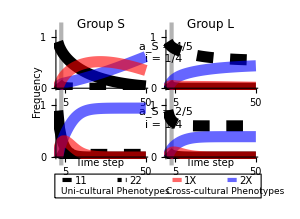

./figures/FigureTrajD.pdf

```mathematica
(*matching pheno freqs: all machis and mestizos, just cross and uni-cult competence*)

(*A************ high in-group affinity *********************************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={8/10,9/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=1/4,(*identity valuation*)
muA=1 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


figaA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figaB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{White,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*B******************** decrease a ******************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=1/4,(*identity valuation*)
muA=1 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figbA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{50,"50"},{5,"5"}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figbB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{White,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];

(******************** assemble plots into Figure ****************************)
FigureTrajD=Panel[
GraphicsGrid[
{{figaA,figaB},{figbA,figbB}},

Spacings->{
{
Scaled[0.4], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0],
Scaled[1.5]
}
},

Frame->True,
FrameStyle->Directive[White],

Prolog->{
{AbsoluteThickness[3],GrayLevel[0.7],Opacity[1],Line[{{111,-8},{111,-470}}]},
{AbsoluteThickness[3],GrayLevel[0.7],Opacity[1],Line[{{472,-8},{472,-470}}]},

(*{AbsoluteThickness[1],Green,Opacity[1],Line[{{108,-8},{108,-470}}]},
{AbsoluteThickness[1],Green,Opacity[1],Line[{{475,-8},{475,-470}}]}*)
},

Epilog->{
Inset[Style["Group S",12],{240,-15}],
Inset[Style["Group L",12],{600,-15}],
Inset[Rotate[Style["Frequency",10],90Degree],{30,-231}],
(*Inset[Rotate[Style["Frequency",10],90Degree],{20,-342}],*)
Inset[Style["Time step",10],{235,-462}],
Inset[Style["Time step",10],{595,-462}],

Inset[Row[{Subscript[Style["a",Italic,8],Style["S",Italic,6]],Style[" = 4/5",8]}],{365,-85},{Left,Center}],
Inset[Row[{Style["i",Italic,8],Style[" = 1/4",8]}],{385,-125},{Left,Center}],

Inset[Row[{Subscript[Style["a",Italic,8],Style["S",Italic,6]],Style[" = 2/5",8]}],{365,-295},{Left,Center}],
Inset[Row[{Style["i",Italic,8],Style[" = 1/4",8]}],{385,-340},{Left,Center}],

x1=-85;
y1=-420;

{EdgeForm[Thin],White,(*Opacity[0.6],*)Rectangle[{175+x1,-78+y1},{850+x1,-155+y1}]},
Inset[Style["11",10],{260+x1,-100+y1}],
Inset[Style["Uni-cultural Phenotypes",9],{195+x1,-135+y1},{Left,Center}],
Inset[Style["22",10],{440+x1,-100+y1}],
Inset[Style["1X",10],{620+x1,-100+y1}],
Inset[Style["Cross-cultural Phenotypes",9],{540+x1,-135+y1},{Left,Center}],
Inset[Style["2X",10],{800+x1,-100+y1}],
{AbsoluteThickness[3],Black,Opacity[1],Line[{{200+x1,-97+y1},{230+x1,-97+y1}}]},
{AbsoluteThickness[3],CapForm["Butt"],Dashing[0.01],Black,Opacity[1],Line[{{380+x1,-97+y1},{410+x1,-97+y1}}]},
{AbsoluteThickness[3],Red,Opacity[0.6],Line[{{560+x1,-97+y1},{590+x1,-97+y1}}]},
{AbsoluteThickness[3],Blue,Opacity[0.6],Line[{{740+x1,-97+y1},{770+x1,-97+y1}}]}
},
ImageSize->300
],(*Graphics Grid*)
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)

Export["./figures/FigureTrajD.pdf",FigureTrajD,"PDF"]
```

## Simulation Trajectories, high identity valuation

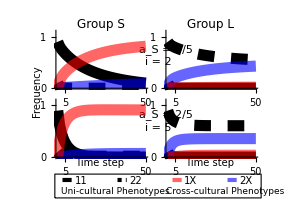

./figures/FigureTrajE.pdf

```mathematica
(*matching pheno freqs: all machis and mestizos, just cross and uni-cult competence, inter-ethnic exp*)

(*A*************** high in-group affinity ******************************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={8/10,9/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=2,(*identity valuation*)
muA=1 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


figaA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figaB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{White,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*B******************** decrease a, increase i ******************)
xcultsim[
matAinit={{9/10,0},{0,1/10}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{1/10,0},{0,9/10}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=5,(*identity valuation*)
muA=1 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figbA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{Black,9}},
Ticks->{{{50,"50"},{5,"5"}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figbB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.01,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{{Black,9},{White,9}},
Ticks->{{{5,"5"},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];

(******************** assemble plots into Figure ****************************)
FigureTrajE=Panel[
GraphicsGrid[
{{figaA,figaB},{figbA,figbB}},

Spacings->{
{
Scaled[0.4], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0],
Scaled[1.5]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["Group S",12],{240,-15}],
Inset[Style["Group L",12],{600,-15}],
Inset[Rotate[Style["Frequency",10],90Degree],{30,-231}],
(*Inset[Rotate[Style["Frequency",10],90Degree],{20,-342}],*)
Inset[Style["Time step",10],{235,-462}],
Inset[Style["Time step",10],{595,-462}],

Inset[Row[{Subscript[Style["a",Italic,8],Style["S",Italic,6]],Style[" = 4/5",8]}],{365,-95},{Left,Center}],
Inset[Row[{Style["i",Italic,8],Style[" = 2",8]}],{385,-135},{Left,Center}],

Inset[Row[{Subscript[Style["a",Italic,8],Style["S",Italic,6]],Style[" = 2/5",8]}],{365,-305},{Left,Center}],
Inset[Row[{Style["i",Italic,8],Style[" = 5",8]}],{385,-350},{Left,Center}],

x1=-85;
y1=-420;

{EdgeForm[Thin],White,(*Opacity[0.6],*)Rectangle[{175+x1,-78+y1},{850+x1,-155+y1}]},
Inset[Style["11",10],{260+x1,-100+y1}],
Inset[Style["Uni-cultural Phenotypes",9],{195+x1,-135+y1},{Left,Center}],
Inset[Style["22",10],{440+x1,-100+y1}],
Inset[Style["1X",10],{620+x1,-100+y1}],
Inset[Style["Cross-cultural Phenotypes",9],{540+x1,-135+y1},{Left,Center}],
Inset[Style["2X",10],{800+x1,-100+y1}],
{AbsoluteThickness[3],Black,Opacity[1],Line[{{200+x1,-97+y1},{230+x1,-97+y1}}]},
{AbsoluteThickness[3],CapForm["Butt"],Dashing[0.01],Black,Opacity[1],Line[{{380+x1,-97+y1},{410+x1,-97+y1}}]},
{AbsoluteThickness[3],Red,Opacity[0.6],Line[{{560+x1,-97+y1},{590+x1,-97+y1}}]},
{AbsoluteThickness[3],Blue,Opacity[0.6],Line[{{740+x1,-97+y1},{770+x1,-97+y1}}]}
},
ImageSize->300
],(*Graphics Grid*)
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)


Export["./figures/FigureTrajE.pdf",FigureTrajE,"PDF"]
```

## Trajectory Sensitivity

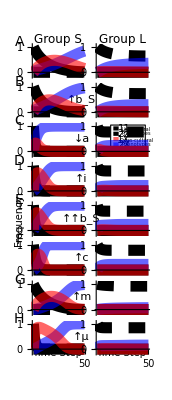

./figures/FigureTrajAll.pdf

```mathematica
(*trajectory sensitivity analysis*)

(*A******************** no power differences *************************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={0,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={8/10,9/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


figaA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{5,""},{50,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figaB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*B******************** power difference ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={8/10,9/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figbA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figbB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];




(*C******************** low affinity ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figcA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figcB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*D******************** identity ***********************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figdA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figdB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*E******************** large power difference ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={5,1},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figeA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figeB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*F******************** high cognitive dissonance ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=9/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figfA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figfB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*G******************** high maintenance ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figgA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figgB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*H******************** high payoff bias ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=3 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

fighA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,"50"},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

fighB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(******************** assemble plots into Figure ****************************)
FigureTrajAll=Panel[
GraphicsGrid[
{{figaA,figaB},{figbA,figbB},{figcA,figcB},{figdA,figdB},
{figeA,figeB},{figfA,figfB},{figgA,figgB},{fighA,fighB}},

Spacings->{
{
Scaled[0.4], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0.3]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["Group S",12],{240,-15}],
Inset[Style["Group L",12],{600,-15}],
Inset[Style["A",14],{20,-30}],
Inset[Style["B",14],{20,-253}],
Inset[Style["C",14],{20,-476}],
Inset[Style["D",14],{20,-699}],
Inset[Style["E",14],{20,-922}],
Inset[Style["F",14],{20,-1145}],
Inset[Style["G",14],{20,-1368}],
Inset[Style["H",14],{20,-1591}],
Inset[Rotate[Style["Frequency",10],90Degree],{20,-1032}],
Inset[Style["Time Step",10],{235,-1782}],
Inset[Style["Time Step",10],{595,-1782}],

Inset[Style[UpArrow["",Subscript[Style["b",Italic,10],Style["S",Italic,8]]]],{370,-353}],
Inset[Style[DownArrow["",Style["a",Italic,10]]],{370,-576}],
Inset[Style[UpArrow["",Style["i",Italic,10]]],{370,-799}],
Inset[Style[UpArrow["","",Subscript[Style["b",Italic,10],Style["S",Italic,8]]]],{370,-1022}],
Inset[Style[UpArrow["",Style["c",Italic,10]]],{370,-1245}],
Inset[Style[UpArrow["",Style["m",Italic,10]]],{370,-1468}],
Inset[Style[UpArrow["",Style["μ",10]]],{370,-1691}], (*type \[Mu ] w/o the space*)

x1=350;
y1=-420;

{EdgeForm[Thin],White,(*Opacity[0.6],*)Rectangle[{185+x1,-78+y1},{380+x1,-210+y1}]},
Inset[Style["11",10],{260+x1,-100+y1}],
Inset[Style["Uni-cultural",5],{330+x1,-105+y1}],
Inset[Style["Phenotypes",5],{330+x1,-125+y1}],
Inset[Style["22",10],{260+x1,-130+y1}],
Inset[Style["1X",10],{260+x1,-160+y1}],
Inset[Style["Cross-cultural",5],{330+x1,-165+y1}],
Inset[Style["Phenotypes",5],{330+x1,-185+y1}],
Inset[Style["2X",10],{260+x1,-190+y1}],
{AbsoluteThickness[3],Black,Opacity[1],Line[{{200+x1,-97+y1},{230+x1,-97+y1}}]},
{AbsoluteThickness[3],CapForm["Butt"],Dashing[0.01],Black,Opacity[1],Line[{{200+x1,-127+y1},{230+x1,-127+y1}}]},
{AbsoluteThickness[3],Red,Opacity[0.6],Line[{{200+x1,-157+y1},{230+x1,-157+y1}}]},
{AbsoluteThickness[3],Blue,Opacity[0.6],Line[{{200+x1,-187+y1},{230+x1,-187+y1}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)

Export["./figures/FigureTrajAll.pdf",FigureTrajAll,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

## Trajectory Sensitivity with greater group size difference

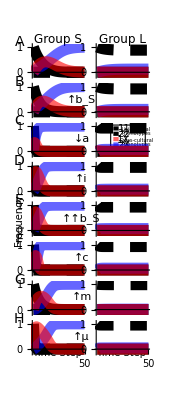

./figures/FigureTrajAllsize.pdf

```mathematica
(*trajectory sensitivity analysis*)

(*A******************** no power differences *************************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={0,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={75/100,95/100},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


figaA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{5,""},{50,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figaB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*B******************** power difference ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={75/100,95/100},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figbA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figbB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];




(*C******************** low affinity ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={25/100,85/100},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figcA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figcB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*D******************** identity ***********************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={25/100,85/100},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figdA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figdB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*E******************** large power difference ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={5,1},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={25/100,85/100},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figeA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figeB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*F******************** high cognitive dissonance ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=9/10,(*cost of coordinating using norm that is not personally held*)
a={25/100,85/100},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figfA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figfB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*G******************** high maintenance ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={25/100,85/100},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figgA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figgB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*H******************** high payoff bias ******************)
xcultsim[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={25/100,85/100},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=3 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

fighA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,"50"},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

fighB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(******************** assemble plots into Figure ****************************)
FigureTrajAllsize=Panel[
GraphicsGrid[
{{figaA,figaB},{figbA,figbB},{figcA,figcB},{figdA,figdB},
{figeA,figeB},{figfA,figfB},{figgA,figgB},{fighA,fighB}},

Spacings->{
{
Scaled[0.4], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0.3]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["Group S",12],{240,-15}],
Inset[Style["Group L",12],{600,-15}],
Inset[Style["A",14],{20,-30}],
Inset[Style["B",14],{20,-253}],
Inset[Style["C",14],{20,-476}],
Inset[Style["D",14],{20,-699}],
Inset[Style["E",14],{20,-922}],
Inset[Style["F",14],{20,-1145}],
Inset[Style["G",14],{20,-1368}],
Inset[Style["H",14],{20,-1591}],
Inset[Rotate[Style["Frequency",10],90Degree],{20,-1032}],
Inset[Style["Time Step",10],{235,-1782}],
Inset[Style["Time Step",10],{595,-1782}],

Inset[Style[UpArrow["",Subscript[Style["b",Italic,10],Style["S",Italic,8]]]],{370,-353}],
Inset[Style[DownArrow["",Style["a",Italic,10]]],{370,-576}],
Inset[Style[UpArrow["",Style["i",Italic,10]]],{370,-799}],
Inset[Style[UpArrow["","",Subscript[Style["b",Italic,10],Style["S",Italic,8]]]],{370,-1022}],
Inset[Style[UpArrow["",Style["c",Italic,10]]],{370,-1245}],
Inset[Style[UpArrow["",Style["m",Italic,10]]],{370,-1468}],
Inset[Style[UpArrow["",Style["μ",10]]],{370,-1691}], (*type \[Mu ] w/o the space*)

x1=350;
y1=-420;

{EdgeForm[Thin],White,(*Opacity[0.6],*)Rectangle[{185+x1,-78+y1},{380+x1,-210+y1}]},
Inset[Style["11",10],{260+x1,-100+y1}],
Inset[Style["Uni-cultural",5],{330+x1,-105+y1}],
Inset[Style["Phenotypes",5],{330+x1,-125+y1}],
Inset[Style["22",10],{260+x1,-130+y1}],
Inset[Style["1X",10],{260+x1,-160+y1}],
Inset[Style["Cross-cultural",5],{330+x1,-165+y1}],
Inset[Style["Phenotypes",5],{330+x1,-185+y1}],
Inset[Style["2X",10],{260+x1,-190+y1}],
{AbsoluteThickness[3],Black,Opacity[1],Line[{{200+x1,-97+y1},{230+x1,-97+y1}}]},
{AbsoluteThickness[3],CapForm["Butt"],Dashing[0.01],Black,Opacity[1],Line[{{200+x1,-127+y1},{230+x1,-127+y1}}]},
{AbsoluteThickness[3],Red,Opacity[0.6],Line[{{200+x1,-157+y1},{230+x1,-157+y1}}]},
{AbsoluteThickness[3],Blue,Opacity[0.6],Line[{{200+x1,-187+y1},{230+x1,-187+y1}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)

Export["./figures/FigureTrajAllsize.pdf",FigureTrajAllsize,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

## Trajectory Sensitivity, simplified model

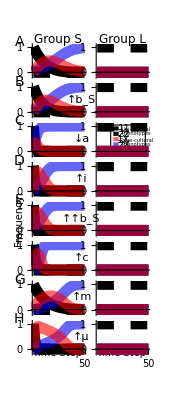

./figures/FigureTrajAllsimp.pdf

```mathematica
(*trajectory sensitivity analysis - simplified model*)

(*A******************** no power differences *************************)
xcultsimsimp[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={0,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={8/10,9/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];

(*Print[matAall //MatrixForm]*)

(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


figaA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{5,""},{50,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figaB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*B******************** power difference ******************)
xcultsimsimp[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={8/10,9/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figbA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figbB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];




(*C******************** low affinity ******************)
xcultsimsimp[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=0,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figcA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figcB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];



(*D******************** identity ***********************)
xcultsimsimp[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figdA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figdB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*E******************** large power difference ******************)
xcultsimsimp[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={5,1},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figeA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figeB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*F******************** high cognitive dissonance ******************)
xcultsimsimp[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=9/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figfA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figfB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*G******************** high maintenance ******************)
xcultsimsimp[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

figgA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,""},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

figgB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,""}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*H******************** power difference, high affinity, majority norm takes over ******************)
xcultsimsimp[
matAinit={{1,0},{0,0}}, (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}},

tmax=50,(*# sims*)
b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={4/10,7/10},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=1,(*identity valuation*)
muA=3 (*effect of a power difference on copying between groups*)
]


(*Plots*)
A11gA=Take[matAall[[All,1]],{1,2*tmax,2}];(*vector of all rows and first column of matAall, then take the first element and every second element after that until the end of the vector*)
A2XgA=Take[matAall[[All,1]],{2,2*tmax,2}];
A1XgA=Take[matAall[[All,2]],{1,2*tmax,2}];
A22gA=Take[matAall[[All,2]],{2,2*tmax,2}];
B11gB=Take[matBall[[All,1]],{1,2*tmax,2}];
B2XgB=Take[matBall[[All,1]],{2,2*tmax,2}];
B1XgB=Take[matBall[[All,2]],{1,2*tmax,2}];
B22gB=Take[matBall[[All,2]],{2,2*tmax,2}];

(*Round[A11gA[[Length[A11gA]]],0.01]*)

(*
Labeled[ListLinePlot[{A11gA,A1XgA,A2XgA,A22gA},
PlotLabel->"Group A",
PlotLegends->{"A11", "A1X","A2X","A22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]

Labeled[ListLinePlot[{B11gB,B1XgB,B2XgB,B22gB},
PlotLabel->"Group B",
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotLegends->{"B11", "B1X","B2X","B22"}],
{"Simulation", "Phenotype Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)

fighA=
ListLinePlot[
{A11gA,A22gA,A2XgA,A1XgA}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,Black},
Ticks->{{{50,"50"},{5,""}},{{0,"0"},{0.5,"0.5"},{1,"1"}}}
];

fighB=
ListLinePlot[
{B11gB,B22gB,B2XgB,B1XgB}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1 x00", "minority group 1 x01",
"majority group 2 x00","majority group 2 x01"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.2,1.1}},
PlotStyle->{{Black,Opacity[1],Thickness[0.02]},{CapForm["Butt"],Dashing[0.03],Black,Opacity[1],Thickness[0.02]},{Blue,Opacity[0.6],Thickness[0.02]},{Red,Opacity[0.6],Thickness[0.02]}},
TicksStyle->{Black,White},
Ticks->{{{5,""},{50,"50"}},{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(*************** assemble plots into Figure ****************************)
FigureTrajAllsimp=Panel[
GraphicsGrid[
{{figaA,figaB},{figbA,figbB},{figcA,figcB},{figdA,figdB},
{figeA,figeB},{figfA,figfB},{figgA,figgB},{fighA,fighB}},

Spacings->{
{
Scaled[0.4], (*horizontal spacing: before, middle, end of row of figures*)
Scaled[0],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical spacing: above, middles, bottom of column of figures*)
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0.3]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["Group S",12],{240,-15}],
Inset[Style["Group L",12],{600,-15}],
Inset[Style["A",14],{20,-30}],
Inset[Style["B",14],{20,-253}],
Inset[Style["C",14],{20,-476}],
Inset[Style["D",14],{20,-699}],
Inset[Style["E",14],{20,-922}],
Inset[Style["F",14],{20,-1145}],
Inset[Style["G",14],{20,-1368}],
Inset[Style["H",14],{20,-1591}],
Inset[Rotate[Style["Frequency",10],90Degree],{20,-1032}],
Inset[Style["Time Step",10],{235,-1782}],
Inset[Style["Time Step",10],{595,-1782}],

Inset[Style[UpArrow["",Subscript[Style["b",Italic,10],Style["S",Italic,8]]]],{370,-353}],
Inset[Style[DownArrow["",Style["a",Italic,10]]],{370,-576}],
Inset[Style[UpArrow["",Style["i",Italic,10]]],{370,-799}],
Inset[Style[UpArrow["","",Subscript[Style["b",Italic,10],Style["S",Italic,8]]]],{370,-1022}],
Inset[Style[UpArrow["",Style["c",Italic,10]]],{370,-1245}],
Inset[Style[UpArrow["",Style["m",Italic,10]]],{370,-1468}],
Inset[Style[UpArrow["",Style["μ",10]]],{370,-1691}], (*type \[Mu ] w/o the space*)

x1=350;
y1=-420;

{EdgeForm[Thin],White,(*Opacity[0.6],*)Rectangle[{185+x1,-78+y1},{380+x1,-210+y1}]},
Inset[Style["11",10],{260+x1,-100+y1}],
Inset[Style["Uni-cultural",5],{330+x1,-105+y1}],
Inset[Style["Phenotypes",5],{330+x1,-125+y1}],
Inset[Style["22",10],{260+x1,-130+y1}],
Inset[Style["1X",10],{260+x1,-160+y1}],
Inset[Style["Cross-cultural",5],{330+x1,-165+y1}],
Inset[Style["Phenotypes",5],{330+x1,-185+y1}],
Inset[Style["2X",10],{260+x1,-190+y1}],
{AbsoluteThickness[3],Black,Opacity[1],Line[{{200+x1,-97+y1},{230+x1,-97+y1}}]},
{AbsoluteThickness[3],CapForm["Butt"],Dashing[0.01],Black,Opacity[1],Line[{{200+x1,-127+y1},{230+x1,-127+y1}}]},
{AbsoluteThickness[3],Red,Opacity[0.6],Line[{{200+x1,-157+y1},{230+x1,-157+y1}}]},
{AbsoluteThickness[3],Blue,Opacity[0.6],Line[{{200+x1,-187+y1},{230+x1,-187+y1}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)

Export["./figures/FigureTrajAllsimp.pdf",FigureTrajAllsimp,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

## Long-run end states

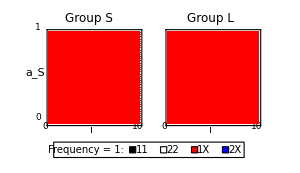

./figures/DensFig.pdf

```mathematica
(*Explore long-run trends*)

Clear[pA11,pA1X,pA2X,pA22,pB11,pB1X,pB2X,pB22,sA,b,c,a,m,i,muW,muB,bA,bB,wA11,wA1X,wA2X,wA22,wB11,wB1X,wB2X,wB22, matA, matB, matAall, matBall,fitA, fitB, fitAall, fitBall,A1Xmat,A2Xmat,B1Xmat,B2Xmat];


aASeq=Range[0,1,1/50];(*in-group affinity increment*)
aBSeq=1-((1-aASeq)*1/2); (* keep group B twice as big as group A *)
iSeq=Range[0,10,1/5];(*group identity valuation increment*)
tmaxAll =100;(*# sims, change this to something like 20 and it will run much faster*)
pgAinitAll={{3/4,0},{0,1/4}}; (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
pgBinitAll={{1/4,0},{0,3/4}};



Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=1, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=1 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{Round[aASeq[[1]]],""},{Round[aASeq[[Length[aASeq]]]],""}},None},{{{iSeq[[1]],"0"},{iSeq[[Length[iSeq]]],"10"}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) , (*Blue*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{Round[aASeq[[1]]],""},{Round[aASeq[[Length[aASeq]]]],""}},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,(*to reverse the shading, now dark is high pA11*)
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel , (*Grey*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{Round[aASeq[[1]]],""},{Round[aASeq[[Length[aASeq]]]],""}},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

(*unfilled white is A22*)

a1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]],"0"},{iSeq[[Length[iSeq]]],"10"}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) , (*Blue*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,(*to reverse the shading, now dark is high pB11*)
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel , (*Grey*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


(*unfilled white is B22*)

a2=Show[B11plot,B2Xplot,B1Xplot];




(*************************************assemble plots into Figure*)

DensFig=Panel[
GraphicsRow[
{a1,a2},
(*Dividers->{False,{1->White,2->White,3->Black, 4->Black, 5->Black, 6->White,7->White}},*)(*{{True,White}, True, True, True, True}},*)

Spacings->{
{
Scaled[0.2], (*horizontal space before, between, after plots*)
Scaled[0.1],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical space above, between, below plots*)
Scaled[0.8]}
},
Frame->True,
FrameStyle->Directive[White],(**)
Epilog->{
Inset[Style["Group S",12],{200,-10}],
Inset[Style["Group L",12],{590,-10}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{25,-183}],
Inset[Style["i",Italic,10],{206,-370}],
Inset[Style["i",Italic,10],{592,-370}],

Inset[Style["1",9],{35,-37}],
Inset[Style["0",9],{35,-330}],
Inset[Style["0",9],{57,-360}],
Inset[Style["10",9],{355,-360}],
Inset[Style["0",9],{443,-360}],
Inset[Style["10",9],{740,-360}],


moveright=620;
moveup=390;

{EdgeForm[Thin],White,Rectangle[{705-moveright,-20-moveup},{1320-moveright,-70-moveup}]},

Inset[Style["Frequency = 1:",10],{810-moveright,-45-moveup}],

{EdgeForm[Thin],Black,Rectangle[{950-moveright,-35-moveup},{970-moveright,-55-moveup}]}, (*{xmin,ymin},{xmax,ymax}*)
Inset[Style["11",10],{990-moveright,-45-moveup}],

{EdgeForm[Thin],White,Rectangle[{1050-moveright,-35-moveup},{1070-moveright,-55-moveup}]},
Inset[Style["22",10],{1090-moveright,-45-moveup}],

{EdgeForm[Thin],Hue[1,1,1,1],Rectangle[{1150-moveright,-35-moveup}, (*Red*){1170-moveright,-55-moveup}]}, 
Inset[Style["1X",10],{1190-moveright,-45-moveup}],

{EdgeForm[Thin],Hue[3.3/5,1,1,1],(*blue*)Rectangle[{1250-moveright,-35-moveup},{1270-moveright,-55-moveup}]},
Inset[Style["2X",10],{1290-moveright,-45-moveup}]
},
ImageSize->300
],(*graphics row*)
Appearance->"Frameless",
Background->White,
FrameMargins->{{5,5},{5,5}}(*-35 last one*)
](*panel*)


(*Export["~/Fig2.eps",Fig2,"EPS"]*)
Export["./figures/DensFig.pdf",DensFig,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

## Color mixture key for density plots

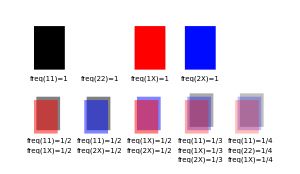

./figures/DensFigKey.pdf

```mathematica
(*4 alleles at equal frequency*)
allEq=Graphics[{
EdgeForm[Thin],White,Rectangle[{0.3,0.3}], (*white, 22*)
EdgeForm[],GrayLevel[1-0.25],Rectangle[{0.2,0.2}],(*black, 11*)
EdgeForm[],Hue[3.3/5,1,1,0.25],Rectangle[{0.1,0.1}], (*blue, 2X*)
EdgeForm[],Hue[1,1,1, 0.25],Rectangle[{0,0}] (*red, 1X*)
}];

(*3 alleles at equal frequency, no 22*)
threeEq=Graphics[{
EdgeForm[{Thin,White}],White,Rectangle[{0.3,0.3}], (*white, 22*)
EdgeForm[],GrayLevel[1-0.333],Rectangle[{0.2,0.2}],(*black, 11*)
EdgeForm[],Hue[3.3/5,1,1,0.333],Rectangle[{0.1,0.1}], (*blue, 2X*)
EdgeForm[],Hue[1,1,1, 0.333],Rectangle[{0,0}] (*red, 1X*)
}];

(*1X and 2X at equal frequency, no 11 or 22*)
xcultEq=Graphics[{
EdgeForm[{Thin,White}],White,Rectangle[{0.3,0.3}], (*white, 22*)
EdgeForm[],Hue[3.3/5,1,1,0.5],Rectangle[{0.1,0.1}], (*blue, 2X*)
EdgeForm[],Hue[1,1,1, 0.5],Rectangle[{0,0}] (*red, 1X*)
}];

(*1X and 11 at equal frequency*)
onesEq=Graphics[{
EdgeForm[{Thin,White}],White,Rectangle[{0.3,0.3}], (*white, 22*)
EdgeForm[],GrayLevel[1-0.5],Rectangle[{0.1,0.1}],(*black, 11*)
EdgeForm[],Hue[1,1,1, 0.5],Rectangle[{0,0}] (*red, 1X*)
}];

(*2X and 11 at equal frequency*)
twooneEq=Graphics[{
EdgeForm[{Thin,White}],White,Rectangle[{0.3,0.3}], (*white, 22*)
EdgeForm[],GrayLevel[1-0.5],Rectangle[{0.1,0.1}],(*black, 11*)
EdgeForm[],Hue[3.3/5,1,1,0.5],Rectangle[{0,0}] (*blue, 2X*)
}];

(*2X*)
twox=Graphics[{
EdgeForm[],Hue[3.3/5,1,1,1],Rectangle[{0,0}], (*blue, 2X*)
}];

(*1X*)
onex=Graphics[{
EdgeForm[],Hue[1,1,1,1],Rectangle[{0,0}] (*red, 1X*)
}];

(*11*)
oneone=Graphics[{
EdgeForm[],GrayLevel[1-1],Rectangle[{0.2,0.2}](*black, 11*)
}];

twotwo=Graphics[{
EdgeForm[Thin],White,Rectangle[{0.3,0.3}] (*white, 22*)
}];

(*************************************assemble plots into Figure*)

DensFigKey=Panel[
GraphicsGrid[
{{oneone,twotwo,onex,twox,""},{onesEq,twooneEq,xcultEq,threeEq,allEq}},

Spacings->{
{
Scaled[0.2], (*horizontal space before, between, after plots*)
Scaled[0.4],
Scaled[0.4],
Scaled[0.4],
Scaled[0.4],
Scaled[0.2]
},
{
Scaled[0.3], (*vertical space above, between, below plots*)
Scaled[0.3],
Scaled[1.1]}
},
Frame->True,
FrameStyle->Directive[White],(**)
Epilog->{
Inset[Style["freq(11)=1",7],{7,-20}],
Inset[Style["freq(22)=1",7],{23,-20}],
Inset[Style["freq(1X)=1",7],{39,-20}],
Inset[Style["freq(2X)=1",7],{55,-20}],

Inset[Style["freq(11)=1/2",7],{7,-40}],
Inset[Style["freq(11)=1/2",7],{23,-40}],
Inset[Style["freq(1X)=1/2",7],{39,-40}],
Inset[Style["freq(11)=1/3",7],{55,-40}],
Inset[Style["freq(11)=1/4",7],{71,-40}],

Inset[Style["freq(1X)=1/2",7],{7,-43}],
Inset[Style["freq(2X)=1/2",7],{23,-43}],
Inset[Style["freq(2X)=1/2",7],{39,-43}],
Inset[Style["freq(1X)=1/3",7],{55,-43}],
Inset[Style["freq(22)=1/4",7],{71,-43}],

Inset[Style["freq(2X)=1/3",7],{55,-46}],
Inset[Style["freq(1X)=1/4",7],{71,-46}],

Inset[Style["freq(2X)=1/4",7],{71,-49}],
},
ImageSize->300
],(*graphics row*)
Appearance->"Frameless",
Background->White,
FrameMargins->{{1,1},{5,5}}(*-35 last one*)
](*panel*)


Export["./figures/DensFigKey.pdf",DensFigKey,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

## Long-run sensitivity

Done part a

Done part b

Done part c

Done part d

Done part e

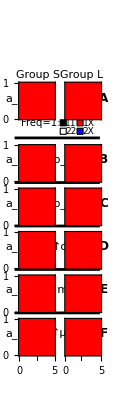

```mathematica
(*Long-run trends sensitivity analysis*)

Clear[pA11,pA1X,pA2X,pA22,pB11,pB1X,pB2X,pB22,sA,b,c,a,m,i,muW,muB,bA,bB,wA11,wA1X,wA2X,wA22,wB11,wB1X,wB2X,wB22, matA, matB, matAall, matBall,fitA, fitB, fitAall, fitBall,A1Xmat,A2Xmat,B1Xmat,B2Xmat];


aASeq=Range[0,1,1/20];(*in-group affinity increment*)
aBSeq=1-((1-aASeq)*1/2); (* keep group B twice as big as group A *)
iSeq=Range[0,5,1/4]; (*group identity valuation interval*)
tmaxAll =100; (*# sims, change this to something like 20 and it will run much faster*)
pgAinitAll={{1,0},{0,0}}; (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
pgBinitAll={{0,0},{0,1}};


(*A********** no power difference ***********************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={0,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) , (*Blue*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

a1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

a2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part a"]


(*B********** low power difference ***********************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

b1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

b2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part b"]


(*C******* high power difference ****************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={5,1},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

c1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

c2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part c"];



(*D********* high c *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=9/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

d1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

d2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part d"];


(*E*********  high m *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

e1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

e2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part e"];



(*F********* high mu *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=3 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

f1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

f2=Show[B11plot,B2Xplot,B1Xplot];



(*assemble plots into Fig 2*)
moveright=30;
moveup=10;

AllDens=Panel[
GraphicsGrid[
{{"",""},{a1,a2},{b1,b2},{c1,c2},{d1,d2},{e1,e2},{f1,f2}},
(*Dividers->{False,{1->White,2->White,3->Black, 4->Black, 5->Black, 6->White,7->White}},*)(*{{True,White}, True, True, True, True}},*)

Spacings->{
{
Scaled[0.2], (*horizontal space before, between, after plots*)
Scaled[0.1],
Scaled[0.4]
},
{
Scaled[0], (*vertical space above, between, below plots*)
Scaled[0],
Scaled[0.5], (*was 0.3*)
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0.2]}
},
Frame->True,
FrameStyle->Directive[White, Opacity[0]],
Epilog->{
Inset[Style["A",12,Bold],{770,-510}],
Inset[Style["B",12,Bold],{770,-1020}],
Inset[Style["C",12,Bold],{770,-1380}],
Inset[Style["D",12,Bold],{770,-1740}],
Inset[Style["E",12,Bold],{770,-2100}],
Inset[Style["F",12,Bold],{770,-2460}],

Inset[Style[UpArrow["",Subscript[Style["b",Italic,6],Style["S",Italic,4]]]],{400,-1020}],
Inset[Style[DoubleUpArrow["",Subscript[Style["b",Italic,6],Style["S",Italic,4]]]],{400,-1380}],
Inset[Style[UpArrow["",Style["c",Italic,6]]],{400,-1740}],
Inset[Style[UpArrow["",Style["m",Italic,6]]],{400,-2100}],
Inset[Style[UpArrow["",Style["μ",6]]],{400,-2460}], (*type \[Mu ] w/o the space*)

Inset[Style["Group S",11],{225,-315}],
Inset[Style["Group L",11],{590,-315}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-510}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1020}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1380}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1740}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-2100}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-2460}],
Inset[Style["i",Italic,10],{220,-2660}],
Inset[Style["i",Italic,10],{590,-2660}],

Inset[Style["Freq=1:",10],{250,-720}],
{EdgeForm[Thin],Black,Rectangle[{440-moveright,-740},{490-moveright,-690}]}, (*{xmin,ymin},{xmax,ymax}*)
Inset[Style["11",9],{530-moveright,-720}],
{EdgeForm[Thin],Hue[1,1,1,1],Rectangle[{580-moveright,-740},{630-moveright,-690}]},
Inset[Style["1X",9],{675-moveright,-720}],

Inset[Style["",10],{250,-780}],
{EdgeForm[Thin],White,Rectangle[{440-moveright,-810},{490-moveright,-760}]},
Inset[Style["22",9],{530-moveright,-790}],
{EdgeForm[Thin],Hue[3.3/5,1,1,1],Rectangle[{580-moveright,-810},{630-moveright,-760}]},
Inset[Style["2X",9],{675-moveright,-790}],

{AbsoluteThickness[2],Black,Line[{{30,-840},{740,-840}}]}, 
{AbsoluteThickness[2],Black,Line[{{30,-1210},{740,-1210}}]}, 
{AbsoluteThickness[2],Black,Line[{{30,-1570},{740,-1570}}]},
{AbsoluteThickness[2],Black,Line[{{30,-1930},{740,-1930}}]},
{AbsoluteThickness[2],Black,Line[{{30,-2290},{740,-2290}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,0}}
](*panel*)

Export["./figures/AllDens.pdf",AllDens,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

## Long-run sensitivity - greater group size differences

```mathematica
(*Long-run trends sensitivity analysis*)

Clear[pA11,pA1X,pA2X,pA22,pB11,pB1X,pB2X,pB22,sA,b,c,a,m,i,muW,muB,bA,bB,wA11,wA1X,wA2X,wA22,wB11,wB1X,wB2X,wB22, matA, matB, matAall, matBall,fitA, fitB, fitAall, fitBall,A1Xmat,A2Xmat,B1Xmat,B2Xmat];


aASeq=Range[0,1,1/20];(*in-group affinity increment*)
aBSeq=1-((1-aASeq)*1/5); (* keep group B five times as big as group A *)
iSeq=Range[0,5,1/4]; (*group identity valuation interval*)
tmaxAll =100; (*# sims, change this to something like 20 and it will run much faster*)
pgAinitAll={{1,0},{0,0}}; (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
pgBinitAll={{0,0},{0,1}};


(*A********** no power difference ***********************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={0,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) , (*Blue*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

a1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

a2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part a"]


(*B********** low power difference ***********************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

b1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

b2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part b"]


(*C******* high power difference ****************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={5,1},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

c1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

c2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part c"];



(*D********* high c *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=9/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

d1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

d2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part d"];


(*E*********  high m *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

e1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

e2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part e"];



(*F********* high mu *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsim[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=3 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

f1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

f2=Show[B11plot,B2Xplot,B1Xplot];



(*assemble plots into Fig 2*)
moveright=30;
moveup=10;

AllDensSize=Panel[
GraphicsGrid[
{{"",""},{a1,a2},{b1,b2},{c1,c2},{d1,d2},{e1,e2},{f1,f2}},
(*Dividers->{False,{1->White,2->White,3->Black, 4->Black, 5->Black, 6->White,7->White}},*)(*{{True,White}, True, True, True, True}},*)

Spacings->{
{
Scaled[0.2], (*horizontal space before, between, after plots*)
Scaled[0.1],
Scaled[0.4]
},
{
Scaled[0], (*vertical space above, between, below plots*)
Scaled[0],
Scaled[0.5], (*was 0.3*)
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0.2]}
},
Frame->True,
FrameStyle->Directive[White, Opacity[0]],
Epilog->{
Inset[Style["A",12,Bold],{770,-510}],
Inset[Style["B",12,Bold],{770,-1020}],
Inset[Style["C",12,Bold],{770,-1380}],
Inset[Style["D",12,Bold],{770,-1740}],
Inset[Style["E",12,Bold],{770,-2100}],
Inset[Style["F",12,Bold],{770,-2460}],

Inset[Style[UpArrow["",Subscript[Style["b",Italic,6],Style["S",Italic,4]]]],{400,-1020}],
Inset[Style[DoubleUpArrow["",Subscript[Style["b",Italic,6],Style["S",Italic,4]]]],{400,-1380}],
Inset[Style[UpArrow["",Style["c",Italic,6]]],{400,-1740}],
Inset[Style[UpArrow["",Style["m",Italic,6]]],{400,-2100}],
Inset[Style[UpArrow["",Style["μ",6]]],{400,-2460}], (*type \[Mu ] w/o the space*)

Inset[Style["Group S",11],{225,-315}],
Inset[Style["Group L",11],{590,-315}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-510}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1020}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1380}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1740}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-2100}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-2460}],
Inset[Style["i",Italic,10],{220,-2660}],
Inset[Style["i",Italic,10],{590,-2660}],

Inset[Style["Freq=1:",10],{250,-720}],
{EdgeForm[Thin],Black,Rectangle[{440-moveright,-740},{490-moveright,-690}]}, (*{xmin,ymin},{xmax,ymax}*)
Inset[Style["11",9],{530-moveright,-720}],
{EdgeForm[Thin],Hue[1,1,1,1],Rectangle[{580-moveright,-740},{630-moveright,-690}]},
Inset[Style["1X",9],{675-moveright,-720}],

Inset[Style["",10],{250,-780}],
{EdgeForm[Thin],White,Rectangle[{440-moveright,-810},{490-moveright,-760}]},
Inset[Style["22",9],{530-moveright,-790}],
{EdgeForm[Thin],Hue[3.3/5,1,1,1],Rectangle[{580-moveright,-810},{630-moveright,-760}]},
Inset[Style["2X",9],{675-moveright,-790}],

{AbsoluteThickness[2],Black,Line[{{30,-840},{740,-840}}]}, 
{AbsoluteThickness[2],Black,Line[{{30,-1210},{740,-1210}}]}, 
{AbsoluteThickness[2],Black,Line[{{30,-1570},{740,-1570}}]},
{AbsoluteThickness[2],Black,Line[{{30,-1930},{740,-1930}}]},
{AbsoluteThickness[2],Black,Line[{{30,-2290},{740,-2290}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,0}}
](*panel*)

Export["./figures/AllDensSize.pdf",AllDensSize,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

Done part a

Done part b

Done part c

Done part d

Done part e

-Graphics-

./figures/AllDensSize.pdf

## Long-run sensitivity, simplified model

```mathematica
(*Long-run trends sensitivity analysis*)

Clear[pA11,pA1X,pA2X,pA22,pB11,pB1X,pB2X,pB22,sA,b,c,a,m,i,muW,muB,bA,bB,wA11,wA1X,wA2X,wA22,wB11,wB1X,wB2X,wB22, matA, matB, matAall, matBall,fitA, fitB, fitAall, fitBall,A1Xmat,A2Xmat,B1Xmat,B2Xmat];


aASeq=Range[0,1,1/20];(*in-group affinity increment*)
aBSeq=1-((1-aASeq)*1/2); (* keep group B twice as big as group A *)
iSeq=Range[0,5,1/4]; (*i increment*)
tmaxAll =100; (*# sims, change this to something like 20 and it will run much faster*)
pgAinitAll={{1,0},{0,0}}; (*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
pgBinitAll={{0,0},{0,1}};

(*A******** no power difference ****************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsimsimp[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={0,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) , (*Blue*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]],""},{iSeq[[Length[iSeq]]],""}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

a1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

a2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part a"]


(*B********** low power difference ***********************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsimsimp[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&) , (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

b1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

b2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part b"]


(*C******* high power difference ****************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsimsimp[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={5,1},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

c1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

c2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part c"];



(*D********* high c *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsimsimp[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=9/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

d1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

d2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part d"];


(*E*********  high m *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsimsimp[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=2 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}} (*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

e1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{{iSeq[[1]]," "},{iSeq[[Length[iSeq]]]," "}},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

e2=Show[B11plot,B2Xplot,B1Xplot];

Print["Done part e"];



(*F********* high mu *********************************************************)

Clear[grpAamat, grpBamat, grpAimat, grpBimat, A11mat, A1Xmat,A2Xmat, A22mat,B11mat, B1Xmat, B2Xmat, B22mat,A1Xplot,A2Xplot,A11plot,B1Xplot,B1Xplot,B11plot];

grpAamat={0,0,0,0};(*initialize matrix of phenotype freqs (columns) for each "a" increment (rows)*)
grpBamat={0,0,0,0};
grpAimat=ConstantArray[0,{Length[aASeq]+1,4}];(*initialize matrix of phenotype freq vectors for each "a" increment (columns) for each "i" increment (rows)*)
grpBimat=ConstantArray[0,{Length[aASeq]+1,4}];

For    [iInc=1,iInc≤Length[iSeq],iInc++,
For    [aInc=1,aInc≤Length[aASeq],aInc++,

xcultsimsimp[
matAinit=pgAinitAll,  
matBinit=pgBinitAll, 

tmax =tmaxAll, 

b={1,0},(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=1/10,(*cost of coordinating using norm that is not personally held*)
a={aASeq[[aInc]],aBSeq[[aInc]]},(*probability of assorting to interact with members of your own group, rather than out-group {aA,AB}*)
m=1/2, (*cost of having to learn and maintain cross-cultural competence*)
i=iSeq[[iInc]],(*identity valuation*)
muA=3 (*effect of a power difference on copying between groups*)
];


(*Print["matAall= ", matAall//MatrixForm];*)
grpAamat=Flatten[ {grpAamat,{Flatten[ Take[matAall,-2] ]} } ]; (*adds a 4-vector of freqs (flattened last 2 rows of matAall matrix) onto matrix of freqs (columns) for each "a" increment (rows)*)
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];(*{rows,columns}*)
(*Print["amat ", MatrixForm[grpAamat]];*)
grpBamat=Flatten[ {grpBamat,{Flatten[ Take[matBall,-2 ] ]} }];
grpAamat=ArrayReshape[grpAamat,{aInc+1,4}];

];(*For aInc*)

(*Print["join ",grpAimat ," with amat ",grpAamat]; *)
grpAimat=Flatten[{grpAimat,grpAamat}]; (*adds a matrix of freqs for each "a" increment to matrix of (matrices of freqs for each "a" increment) for each i increment*)
grpAimat=ArrayReshape[grpAimat,{iInc+1,aInc,4}];(*{rows,columns,depth}*)
(*Print["imat", MatrixForm[grpAimat]];*)
grpBimat=Flatten[{grpBimat,grpBamat}];
grpBimat=ArrayReshape[grpBimat,{iInc+1,aInc,4}];

grpAamat={0,0,0,0};(*re-initialize "a" matrices*)
grpBamat={0,0,0,0};

]; (*For iInc*)


(*grpAimat //MatrixForm *)
grpAimat=Transpose[grpAimat]; (* now "a" rows and "i" columns*)
grpAimat=grpAimat[[2 ;;,2;;]];(*delete junk row and column*)
Round[grpAimat,0.01] //MatrixForm;

A11mat=grpAimat[[All,All,1]]; (*matrix of pA11 for all "a" rows and "i" columns*)
A1Xmat=grpAimat[[All,All,2]]; 
A2Xmat=grpAimat[[All,All,3]]; 
A22mat=grpAimat[[All,All,4]]; 

Round[A11mat,0.01] //MatrixForm;
Round[A1Xmat,0.01] //MatrixForm;
Round[A2Xmat,0.01] //MatrixForm;
Round[A22mat,0.01] //MatrixForm;

(*grpBimat //MatrixForm;*)
grpBimat=Transpose[grpBimat];
grpBimat=grpBimat[[2 ;;,2;;]]; (*delete junk row and column*)
grpBimat //MatrixForm;

B11mat=grpBimat[[All,All,1]]; (*matrix of pB11 for all "a" rows and "i" columns*)
B1Xmat=grpBimat[[All,All,2]];
B2Xmat=grpBimat[[All,All,3]];
B22mat=grpBimat[[All,All,4]];

(*
Labeled[ListLinePlot[{A1Xmat[[All,1]],
				A1Xmat[[All,3]],
				A1Xmat[[All,5]],
				A1Xmat[[All,7]],
				A1Xmat[[All,9]]}, 
PlotLabel->"Group A",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "A1X Frequency"},
{Bottom, Left}, RotateLabel -> True]


Labeled[ListLinePlot[{B2Xmat[[All,1]],
				B2Xmat[[All,3]],
				B2Xmat[[All,5]],
				B2Xmat[[All,7]],
				B2Xmat[[All,9]]}, 
PlotLabel->"Group B",
PlotLegends->{"i=0",
			"i=2",
			"i=4",
			"i=6",
			"i=8"},
PlotRange->{{0,Length[aASeq]},{0,1}}],
{"In-group affinity (a) from 0 to 1", "B2X Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


A1Xplot=(*Labeled[*)
ListDensityPlot[
A1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}}, (* {{xmin,xmax},{ymin,ymax}}*)
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


A2Xplot=(*Labeled[*)
ListDensityPlot[
A2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


A11plot=(*Labeled[*)
ListDensityPlot[
1-A11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{Round[aASeq[[1]]],Round[aASeq[[Length[aASeq]]]]},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}(*ticks {{left,right},{bottom,top}*)
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

f1=Show[A11plot,A2Xplot,A1Xplot];


B1Xplot=(*Labeled[*)
ListDensityPlot[
B1Xmat, 
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->(Hue[1,1,1,#]&), (*Red*)
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"","a"}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*);


B2Xplot=(*Labeled[*)
ListDensityPlot[
B2Xmat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> (Hue[3.3/5,1,1,#]&) ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);


B11plot=(*Labeled[*)
ListDensityPlot[
1-B11mat,
(*MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction-> GrayLevel ,
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{iSeq[[1]],iSeq[[Length[iSeq]]]},{aASeq[[1]],aASeq[[Length[aASeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{aASeq[[1]],""},{aASeq[[Length[aASeq]]],""}},None},{{Round[iSeq[[1]]],Round[iSeq[[Length[iSeq]]]]},None}}
(*FrameLabel->{"",""}*)
](*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*);

f2=Show[B11plot,B2Xplot,B1Xplot];



(*assemble plots into Fig 2*)
moveright=30;
moveup=10;

AllDenssimp=Panel[
GraphicsGrid[
{{"",""},{a1,a2},{b1,b2},{c1,c2},{d1,d2},{e1,e2},{f1,f2}},
(*Dividers->{False,{1->White,2->White,3->Black, 4->Black, 5->Black, 6->White,7->White}},*)(*{{True,White}, True, True, True, True}},*)

Spacings->{
{
Scaled[0.2], (*horizontal space before, between, after plots*)
Scaled[0.1],
Scaled[0.4]
},
{
Scaled[0], (*vertical space above, between, below plots*)
Scaled[0],
Scaled[0.5], (*was 0.3*)
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0.2]}
},
Frame->True,
FrameStyle->Directive[White, Opacity[0]],
Epilog->{
Inset[Style["A",12,Bold],{770,-510}],
Inset[Style["B",12,Bold],{770,-1020}],
Inset[Style["C",12,Bold],{770,-1380}],
Inset[Style["D",12,Bold],{770,-1740}],
Inset[Style["E",12,Bold],{770,-2100}],
Inset[Style["F",12,Bold],{770,-2460}],

Inset[Style[UpArrow["",Subscript[Style["b",Italic,6],Style["S",Italic,4]]]],{400,-1020}],
Inset[Style[DoubleUpArrow["",Subscript[Style["b",Italic,6],Style["S",Italic,4]]]],{400,-1380}],
Inset[Style[UpArrow["",Style["c",Italic,6]]],{400,-1740}],
Inset[Style[UpArrow["",Style["m",Italic,6]]],{400,-2100}],
Inset[Style[UpArrow["",Style["μ",6]]],{400,-2460}], (*type \[Mu ] w/o the space*)

Inset[Style["Group S",11],{225,-315}],
Inset[Style["Group L",11],{590,-315}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-510}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1020}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1380}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-1740}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-2100}],
Inset[Subscript[Style["a",Italic,10],Style["S",Italic,6]],{35,-2460}],
Inset[Style["i",Italic,10],{220,-2660}],
Inset[Style["i",Italic,10],{590,-2660}],

Inset[Style["Freq=1:",10],{250,-720}],
{EdgeForm[Thin],Black,Rectangle[{440-moveright,-740},{490-moveright,-690}]}, (*{xmin,ymin},{xmax,ymax}*)
Inset[Style["11",9],{530-moveright,-720}],
{EdgeForm[Thin],Hue[1,1,1,1],Rectangle[{580-moveright,-740},{630-moveright,-690}]},
Inset[Style["1X",9],{675-moveright,-720}],

Inset[Style["",10],{250,-780}],
{EdgeForm[Thin],White,Rectangle[{440-moveright,-810},{490-moveright,-760}]},
Inset[Style["22",9],{530-moveright,-790}],
{EdgeForm[Thin],Hue[3.3/5,1,1,1],Rectangle[{580-moveright,-810},{630-moveright,-760}]},
Inset[Style["2X",9],{675-moveright,-790}],

{AbsoluteThickness[2],Black,Line[{{30,-840},{740,-840}}]}, 
{AbsoluteThickness[2],Black,Line[{{30,-1210},{740,-1210}}]}, 
{AbsoluteThickness[2],Black,Line[{{30,-1570},{740,-1570}}]},
{AbsoluteThickness[2],Black,Line[{{30,-1930},{740,-1930}}]},
{AbsoluteThickness[2],Black,Line[{{30,-2290},{740,-2290}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,0}}
](*panel*)

Export["./figures/AllDenssimp.pdf",AllDenssimp,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

Done part a

Done part b

General::munfl: («331»)/0.01 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: («332»)/0.01 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: («333»)/0.01 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: («331»)/0.01 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: («332»)/0.01 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: («333»)/0.01 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Done part c

Done part d

Done part e

General::munfl: («341»)/0.01 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: («342»)/0.01 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: («341»)/0.01 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: («342»)/0.01 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

./figures/AllDenssimp.pdf

## Field plots

```mathematica
(************** Field plots ******************)

interv=0.05; (*0.05;*) (*plotting ranges, change step sizes to 0.1 to make it run faster*)
A22freqs=Range[0,1,interv]; 
A1Xfreqs=Range[0,1,interv];
A2Xfreqs=Range[0,1,interv];

initA22={-100}; (*initialize vectors with junk*)
initA1X={-100};
initA2X={-100};

(* get starting frequencies *)
For    [z3=1,z3≤Length[A22freqs],z3++,
For    [z2=1,z2≤Length[A1Xfreqs],z2++,
For    [z1=1,z1≤Length[A2Xfreqs],z1++,

(*only keep triples in the simplex*)
If[(A22freqs[[z3]]+A1Xfreqs[[z2]]+A2Xfreqs[[z1]])==1,
{
If[A1Xfreqs[[z2]]>0,{ (*don't put arrows on bottom equilib line*)
initA22=Append[initA22,A22freqs[[z3]]],
initA1X=Append[initA1X,A1Xfreqs[[z2]]],
initA2X=Append[initA2X,A2Xfreqs[[z1]]]
}](*if*)
}
] (*if*)

] (*x1*)
](*x2*)
](*x3*)

initA22=initA22[[2;;Length[initA22]]]; (*get rid of first junk value*)
initA1X=initA1X[[2;;Length[initA1X]]];
initA2X=initA2X[[2;;Length[initA2X]]];

tmaxfield=10; (*10*) (* trajectory length *)



(*A************** low i ***********************)

bIn={1,0};(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
cIn=1/10;(*cost of coordinating using norm that is not personally held*)
aIn={4/10,7/10};(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
mIn=1; (*cost of having to learn and maintain cross-cultural competence*)
iIn=4;(*identity valuation*)
muAIn=1;(*effect of a power difference on copying between groups*)


coords={ConstantArray[{-100,-100, -100},tmaxfield+1]}; (*initialize with junk*)

For    [x1=1,x1≤Length[initA22],x1++,

xcultsimsimp[
matAinit={{0,initA1X[[x1]]},{initA2X[[x1]],initA22[[x1]]}},(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}}, (*initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)

tmax =tmaxfield,

b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsim*)

Clear[A2XA22coords,A1Xcoords,A2XA22A1Xcoords];

(*Print[matAall];*)

A2XA22coords=Take[matAall,{2,2*(tmax+1),2}]; (* make subset matrix by taking second row and every second row after that until end of matAall, which gives freqs of A2X and A22 in the trajectory *)
A1Xcoords=Take[matAall[[All,2]],{1,2*(tmax+1),2}]; (* make vector of every first element in the second column of matAall, which is freq of A1X in the trajectory *)
A2XA22A1Xcoords=MapThread[Append,{A2XA22coords,A1Xcoords}]; (* joins elements of A1X vector with corresponding pair of A2X and A22 *)
coords=Append[coords,A2XA22A1Xcoords](* make growing matrix of trajectory matrices *)

(*Print["Trajectory ", x1, " of ", Length[initA22]];*)

];(*for x1*)

coords=coords[[2;;Dimensions[coords][[1]],All]]; (* get rid of first junk trajectory *)
coords//MatrixForm;
coords[[All,1]]//MatrixForm;
coords[[All,Dimensions[coords][[2]]]]//MatrixForm;



Print["Done trajectories, begin solve at ", DateString[]];

xcultsolve[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsolve*)

(*
(*equilib stability test plot*)
stabplot=ListLinePlot[{unstabList,
stabList,
Transpose[{equiLineCoords[[All,1]],ConstantArray[1,Length[unstabList[[All,1]]]]}]},
PlotRange->{{0,unstabList[[Length[unstabList[[All,1]]],1]]},{0,2}},
PlotLabel->"d[pA1Xprime]/d[pA1X] at Equilibria",
PlotLabels->{"Unstable","Stable"},
AxesLabel->{"pA22",""},
PlotStyle->{Blue,Red,Black}];
Show[stabplot]
*)


Print["A Finished solve at ", DateString[]];

Clear[plot0,plotmat,plotTemp,equilibplot0,eplotmat,equilibplotTemp,plotfieldb];



(* trajectory plot *)

plot0=Show[background, (* plot one trajectory *)
(*Graphics@triangleTicks[],*) (* https://mathematica.stackexchange.com/questions/39733/how-to-plot-ternary-density-plots/85899#85899 *)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at beginning and end of trajectory*)
Arrow[ternaryToCartesian@@@coords[[1,All]]],(* data input to ternaryToCartesian = matrix of triples for trajectory*)
Text[Style[" S2X",Black,10],{0,-0.05}],
Text[Style["S22 ",Black,10],{1,-0.05}],
Text[Style[" ",Black,10],{0.5,3^0.5/2+0.1}],(*extra vertical space*)
Text[Style["S1X",Black,10],{0.5,3^0.5/2+0.08}]
}
],
AspectRatio->1] ;

plotmat=plot0;

For    [x3=2,x3≤Dimensions[coords][[1]],x3++,

plotTemp=Show[(*background,*)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at 4 points along trajectory*)
Arrow[ternaryToCartesian@@@coords[[x3,All]]]}
], (* data = matrix of triples for trajectory*)
AspectRatio->1];

plotmat={plotmat,plotTemp};

];(*for x3*)

(*Show[plotmat]*)




(* equilibria plot *)
If[Length[equiLineCoords]>0,{ (*if equlibria exist*)

equiLineCoordsUnstable=equiLineCoords[[All,{4,1,2}]]; (*order: A2X,A22,A1X*)
equiLineCoordsStable=equiLineCoords[[All,{5,1,3}]];
(*Print[equiLineCoordsUnstable//MatrixForm];
Print[equiLineCoordsStable//MatrixForm];*)

(*convert line points to cartesian*)
UnstablelinePointsCart={{-100,-100,-100}};
StablelinePointsCart={{-100,-100,-100}};
For    [y2=1,y2≤Length[equiLineCoordsUnstable],y2++, 
UnstablelinePointsCart=Append[UnstablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsUnstable[[y2,All]]}]];
StablelinePointsCart=Append[StablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsStable[[y2,All]]}]];
];(*y2*)
UnstablelinePointsCart=UnstablelinePointsCart[[2;;Length[UnstablelinePointsCart]]]; (*get rid of junk first row*)
StablelinePointsCart=StablelinePointsCart[[2;;Length[StablelinePointsCart]]];

equilibplot0=Show[(*background,*)
Graphics[{Blue,Thickness[0.01],Line[UnstablelinePointsCart]}],
Graphics[{Red,Thickness[0.01],Line[StablelinePointsCart]}],
Graphics[{PointSize[0.04],Blue, Opacity[0.99],
Point[ternaryToCartesian@@@{pA2XmaxEqui}]}],
Graphics[{PointSize[0.04],Black, Opacity[0.99],
Point[ternaryToCartesian@@@{pA22maxEqui}]}],
AspectRatio->1] ;

(*Print["pA2XmaxEqui={A2X,A22,A1X}= ", pA2XmaxEqui, " and pA22maxEqui= ",pA22maxEqui];*)

eplotmat=equilibplot0;

(*
For    [x4=2,x4≤Dimensions[points][[1]],x4++,

equilibplotTemp=Show[(*background,*)
Graphics[{PointSize[0.06],Blue, Opacity[0.8],
Point[ternaryToCartesian@@@{points[[x4,All]]}]}
], (* data = matrix of triples for equilibs*)
AspectRatio->1];

eplotmat={eplotmat,equilibplotTemp};

];(*for x4*)
*)

(*Show[eplotmat]*)


plotfieldA=Show[ plotmat,eplotmat];
},{
plotfieldA=Show[ plotmat];
}];(*if*)



(*Region of invasion resistance*)
Clear[invplot0,iplotmat,invplotTemp,i,pA11,pA1X,pA2X,pB22,pB2X,pB1X];

xcultinvade[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
itest=iIn,(*identity valuation*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
muA=muAIn(*strength of percieved payoff bias on copying*)
];(*xcultinvade*)


If[Length[linePointsCart]>0,{ (*if region exist*)
invplot0=Show[background,
Graphics[{EdgeForm[],Black,Opacity[0.3],Polygon[regionpoints]}],
AspectRatio->1];
plotfieldA=Show[ invplot0,plotfieldA]; 
}];

(*plotfieldA*)



(*B************ higher i ************************)

bIn={1,0};(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
cIn=1/10;(*cost of coordinating using norm that is not personally held*)
aIn={4/10,7/10};(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
mIn=2; (*cost of having to learn and maintain cross-cultural competence*)
iIn=5;(*identity valuation*)
muAIn=1;(*effect of a power difference on copying between groups*)


coords={ConstantArray[{-100,-100, -100},tmaxfield+1]}; (*initialize with junk*)

For    [x1=1,x1≤Length[initA22],x1++,

xcultsimsimp[
matAinit={{0,initA1X[[x1]]},{initA2X[[x1]],initA22[[x1]]}},(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}}, (*initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)

tmax =tmaxfield,

b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsim*)

Clear[A2XA22coords,A1Xcoords,A2XA22A1Xcoords];

(*Print[matAall];*)

A2XA22coords=Take[matAall,{2,2*(tmax+1),2}]; (* make subset matrix by taking second row and every second row after that until end of matAall, which gives freqs of A2X and A22 in the trajectory *)
A1Xcoords=Take[matAall[[All,2]],{1,2*(tmax+1),2}]; (* make vector of every first element in the second column of matAall, which is freq of A1X in the trajectory *)
A2XA22A1Xcoords=MapThread[Append,{A2XA22coords,A1Xcoords}]; (* joins elements of A1X vector with corresponding pair of A2X and A22 *)
coords=Append[coords,A2XA22A1Xcoords](* make growing matrix of trajectory matrices *)

(*Print["Trajectory ", x1, " of ", Length[initA22]];*)

];(*for x1*)

coords=coords[[2;;Dimensions[coords][[1]],All]]; (* get rid of first junk trajectory *)
coords//MatrixForm;
coords[[All,1]]//MatrixForm;
coords[[All,Dimensions[coords][[2]]]]//MatrixForm;



Print["Done trajectories, begin solve at ", DateString[]];

xcultsolve[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsolve*)

(*
(*equilib stability test plot*)
stabplot=ListLinePlot[{unstabList,
stabList,
Transpose[{equiLineCoords[[All,1]],ConstantArray[1,Length[unstabList[[All,1]]]]}]},
PlotRange->{{0,unstabList[[Length[unstabList[[All,1]]],1]]},{0,2}},
PlotLabel->"d[pA1Xprime]/d[pA1X] at Equilibria",
PlotLabels->{"Unstable","Stable"},
AxesLabel->{"pA22",""},
PlotStyle->{Blue,Red,Black}];
Show[stabplot]
*)


Print["B Finished solve at ", DateString[]];

Clear[plot0,plotmat,plotTemp,equilibplot0,eplotmat,equilibplotTemp,plotfieldb];



(* trajectory plot *)

plot0=Show[background, (* plot one trajectory *)
(*Graphics@triangleTicks[],*) (* https://mathematica.stackexchange.com/questions/39733/how-to-plot-ternary-density-plots/85899#85899 *)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at beginning and end of trajectory*)
Arrow[ternaryToCartesian@@@coords[[1,All]]],(* data input to ternaryToCartesian = matrix of triples for trajectory*)
Text[Style[" S2X",Black,10],{0,-0.05}],
Text[Style["S22 ",Black,10],{1,-0.05}],
Text[Style[" ",Black,10],{0.5,3^0.5/2+0.1}],(*extra vertical space*)
Text[Style["S1X",Black,10],{0.5,3^0.5/2+0.08}]
}
],
AspectRatio->1] ;

plotmat=plot0;

For    [x3=2,x3≤Dimensions[coords][[1]],x3++,

plotTemp=Show[(*background,*)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at 4 points along trajectory*)
Arrow[ternaryToCartesian@@@coords[[x3,All]]]}
], (* data = matrix of triples for trajectory*)
AspectRatio->1];

plotmat={plotmat,plotTemp};

];(*for x3*)

(*Show[plotmat]*)




(* equilibria plot *)
If[Length[equiLineCoords]>0,{ (*if equlibria exist*)

equiLineCoordsUnstable=equiLineCoords[[All,{4,1,2}]]; (*order: A2X,A22,A1X*)
equiLineCoordsStable=equiLineCoords[[All,{5,1,3}]];
(*Print[equiLineCoordsUnstable//MatrixForm];
Print[equiLineCoordsStable//MatrixForm];*)

(*convert line points to cartesian*)
UnstablelinePointsCart={{-100,-100,-100}};
StablelinePointsCart={{-100,-100,-100}};
For    [y2=1,y2≤Length[equiLineCoordsUnstable],y2++, 
UnstablelinePointsCart=Append[UnstablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsUnstable[[y2,All]]}]];
StablelinePointsCart=Append[StablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsStable[[y2,All]]}]];
];(*y2*)
UnstablelinePointsCart=UnstablelinePointsCart[[2;;Length[UnstablelinePointsCart]]]; (*get rid of junk first row*)
StablelinePointsCart=StablelinePointsCart[[2;;Length[StablelinePointsCart]]];

equilibplot0=Show[(*background,*)
Graphics[{Blue,Thickness[0.01],Line[UnstablelinePointsCart]}],
Graphics[{Red,Thickness[0.01],Line[StablelinePointsCart]}],
Graphics[{PointSize[0.04],Blue, Opacity[0.99],
Point[ternaryToCartesian@@@{pA2XmaxEqui}]}],
Graphics[{PointSize[0.04],Black, Opacity[0.99],
Point[ternaryToCartesian@@@{pA22maxEqui}]}],
AspectRatio->1] ;

(*Print["pA2XmaxEqui={A2X,A22,A1X}= ", pA2XmaxEqui, " and pA22maxEqui= ",pA22maxEqui];*)

eplotmat=equilibplot0;

(*
For    [x4=2,x4≤Dimensions[points][[1]],x4++,

equilibplotTemp=Show[(*background,*)
Graphics[{PointSize[0.06],Blue, Opacity[0.8],
Point[ternaryToCartesian@@@{points[[x4,All]]}]}
], (* data = matrix of triples for equilibs*)
AspectRatio->1];

eplotmat={eplotmat,equilibplotTemp};

];(*for x4*)
*)

(*Show[eplotmat]*)


plotfieldB=Show[ plotmat,eplotmat];
},{
plotfieldB=Show[ plotmat];
}];(*if*)



(*Region of invasion resistance*)
Clear[invplot0,iplotmat,invplotTemp,i,pA11,pA1X,pA2X,pB22,pB2X,pB1X];

xcultinvade[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
itest=iIn,(*identity valuation*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
muA=muAIn(*strength of percieved payoff bias on copying*)
];(*xcultinvade*)


If[Length[linePointsCart]>0,{ (*if region exist*)
invplot0=Show[background,
Graphics[{EdgeForm[],Black,Opacity[0.3],Polygon[regionpoints]}],
AspectRatio->1];
plotfieldB=Show[ invplot0,plotfieldB]; 
}];

(*plotfieldB*)




(*C*********** highest i ********************)

bIn={1,0};(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
cIn=1/10;(*cost of coordinating using norm that is not personally held*)
aIn={4/10,7/10};(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
mIn=6; (*cost of having to learn and maintain cross-cultural competence*)
iIn=10;(*identity valuation*)
muAIn=1;(*effect of a power difference on copying between groups*)


coords={ConstantArray[{-100,-100, -100},tmaxfield+1]}; (*initialize with junk*)

For    [x1=1,x1≤Length[initA22],x1++,

xcultsimsimp[
matAinit={{0,initA1X[[x1]]},{initA2X[[x1]],initA22[[x1]]}},(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}}, (*initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)

tmax =tmaxfield,

b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsim*)

Clear[A2XA22coords,A1Xcoords,A2XA22A1Xcoords];

(*Print[matAall];*)

A2XA22coords=Take[matAall,{2,2*(tmax+1),2}]; (* make subset matrix by taking second row and every second row after that until end of matAall, which gives freqs of A2X and A22 in the trajectory *)
A1Xcoords=Take[matAall[[All,2]],{1,2*(tmax+1),2}]; (* make vector of every first element in the second column of matAall, which is freq of A1X in the trajectory *)
A2XA22A1Xcoords=MapThread[Append,{A2XA22coords,A1Xcoords}]; (* joins elements of A1X vector with corresponding pair of A2X and A22 *)
coords=Append[coords,A2XA22A1Xcoords](* make growing matrix of trajectory matrices *)

(*Print["Trajectory ", x1, " of ", Length[initA22]];*)

];(*for x1*)

coords=coords[[2;;Dimensions[coords][[1]],All]]; (* get rid of first junk trajectory *)
coords//MatrixForm;
coords[[All,1]]//MatrixForm;
coords[[All,Dimensions[coords][[2]]]]//MatrixForm;



Print["Done trajectories, begin solve at ", DateString[]];

xcultsolve[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsolve*)

(*
(*equilib stability test plot*)
stabplot=ListLinePlot[{unstabList,
stabList,
Transpose[{equiLineCoords[[All,1]],ConstantArray[1,Length[unstabList[[All,1]]]]}]},
PlotRange->{{0,unstabList[[Length[unstabList[[All,1]]],1]]},{0,2}},
PlotLabel->"d[pA1Xprime]/d[pA1X] at Equilibria",
PlotLabels->{"Unstable","Stable"},
AxesLabel->{"pA22",""},
PlotStyle->{Blue,Red,Black}];
Show[stabplot]
*)


Print["C Finished solve at ", DateString[]];

Clear[plot0,plotmat,plotTemp,equilibplot0,eplotmat,equilibplotTemp,plotfieldb];



(* trajectory plot *)

plot0=Show[background, (* plot one trajectory *)
(*Graphics@triangleTicks[],*) (* https://mathematica.stackexchange.com/questions/39733/how-to-plot-ternary-density-plots/85899#85899 *)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at beginning and end of trajectory*)
Arrow[ternaryToCartesian@@@coords[[1,All]]],(* data input to ternaryToCartesian = matrix of triples for trajectory*)
Text[Style[" S2X",Black,10],{0,-0.05}],
Text[Style["S22 ",Black,10],{1,-0.05}],
Text[Style[" ",Black,10],{0.5,3^0.5/2+0.1}],(*extra vertical space*)
Text[Style["S1X",Black,10],{0.5,3^0.5/2+0.08}]
}
],
AspectRatio->1] ;

plotmat=plot0;

For    [x3=2,x3≤Dimensions[coords][[1]],x3++,

plotTemp=Show[(*background,*)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at 4 points along trajectory*)
Arrow[ternaryToCartesian@@@coords[[x3,All]]]}
], (* data = matrix of triples for trajectory*)
AspectRatio->1];

plotmat={plotmat,plotTemp};

];(*for x3*)

(*Show[plotmat]*)




(* equilibria plot *)
If[Length[equiLineCoords]>0,{ (*if equlibria exist*)

equiLineCoordsUnstable=equiLineCoords[[All,{4,1,2}]]; (*order: A2X,A22,A1X*)
equiLineCoordsStable=equiLineCoords[[All,{5,1,3}]];
(*Print[equiLineCoordsUnstable//MatrixForm];
Print[equiLineCoordsStable//MatrixForm];*)

(*convert line points to cartesian*)
UnstablelinePointsCart={{-100,-100,-100}};
StablelinePointsCart={{-100,-100,-100}};
For    [y2=1,y2≤Length[equiLineCoordsUnstable],y2++, 
UnstablelinePointsCart=Append[UnstablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsUnstable[[y2,All]]}]];
StablelinePointsCart=Append[StablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsStable[[y2,All]]}]];
];(*y2*)
UnstablelinePointsCart=UnstablelinePointsCart[[2;;Length[UnstablelinePointsCart]]]; (*get rid of junk first row*)
StablelinePointsCart=StablelinePointsCart[[2;;Length[StablelinePointsCart]]];

equilibplot0=Show[(*background,*)
Graphics[{Blue,Thickness[0.01],Line[UnstablelinePointsCart]}],
Graphics[{Red,Thickness[0.01],Line[StablelinePointsCart]}],
Graphics[{PointSize[0.04],Blue, Opacity[0.99],
Point[ternaryToCartesian@@@{pA2XmaxEqui}]}],
Graphics[{PointSize[0.04],Black, Opacity[0.99],
Point[ternaryToCartesian@@@{pA22maxEqui}]}],
AspectRatio->1] ;

(*Print["pA2XmaxEqui={A2X,A22,A1X}= ", pA2XmaxEqui, " and pA22maxEqui= ",pA22maxEqui];*)

eplotmat=equilibplot0;

(*
For    [x4=2,x4≤Dimensions[points][[1]],x4++,

equilibplotTemp=Show[(*background,*)
Graphics[{PointSize[0.06],Blue, Opacity[0.8],
Point[ternaryToCartesian@@@{points[[x4,All]]}]}
], (* data = matrix of triples for equilibs*)
AspectRatio->1];

eplotmat={eplotmat,equilibplotTemp};

];(*for x4*)
*)

(*Show[eplotmat]*)


plotfieldC=Show[ plotmat,eplotmat];
},{
plotfieldC=Show[ plotmat]; (*if no non-trivial equilibria*)
}];(*if*)



(*Region of invasion resistance*)
Clear[invplot0,iplotmat,invplotTemp,i,pA11,pA1X,pA2X,pB22,pB2X,pB1X];

xcultinvade[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
itest=iIn,(*identity valuation*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
muA=muAIn(*strength of percieved payoff bias on copying*)
];(*xcultinvade*)


If[Length[linePointsCart]>0,{ (*if region exist*)
invplot0=Show[background,
Graphics[{EdgeForm[],Black,Opacity[0.3],Polygon[regionpoints]}],
AspectRatio->1];
plotfieldC=Show[ invplot0,plotfieldC]; 
}];


(*plotfieldA
plotfieldB
plotfieldC*)

(*************************************assemble plots into Figure*)
FieldFig=Panel[
GraphicsRow[
{plotfieldA,plotfieldB,plotfieldC},
(*Dividers->{False,{1->White,2->White,3->Black, 4->Black, 5->Black, 6->White,7->White}},*)(*{{True,White}, True, True, True, True}},*)

Spacings->{
{
Scaled[0.05], (*horizontal space before, between, after plots*)
Scaled[0.05],
Scaled[0.05],
Scaled[0.05]
},
{
Scaled[0.05], (*vertical space above, between, below plots*)
Scaled[0.05]}
},
Frame->True,
FrameStyle->Directive[White],(**)
Epilog->{
Inset[Row[{Style["i",Italic,10],Style[" = 4",10]}],{80,-80},{Left,Center}],
Inset[Row[{Style["i",Italic,10],Style[" = 5",10]}],{460,-80},{Left,Center}],
Inset[Row[{Style["i",Italic,10],Style[" = 10",10]}],{840,-80},{Left,Center}],
Inset[Row[{Style["m",Italic,10],Style[" = 1",10]}],{70,-110},{Left,Center}],
Inset[Row[{Style["m",Italic,10],Style[" = 2",10]}],{450,-110},{Left,Center}],
Inset[Row[{Style["m",Italic,10],Style[" = 6",10]}],{830,-110},{Left,Center}]

},
ImageSize->650
], (*graphics row*)
Appearance->"Frameless",
Background->White,
FrameMargins->{{5,5},{5,5}}
](*panel*)


(*Export["~/Fig2.eps",Fig2,"EPS"]*)
Export["./figures/FieldFig.pdf",FieldFig,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

Done trajectories, begin solve at Thu 1 Oct 2020 13:00:08

A Finished solve at Thu 1 Oct 2020 13:01:44

Done trajectories, begin solve at Thu 1 Oct 2020 13:01:52

B Finished solve at Thu 1 Oct 2020 13:03:32

Done trajectories, begin solve at Thu 1 Oct 2020 13:03:39

C Finished solve at Thu 1 Oct 2020 13:05:31

-Graphics-

./figures/FieldFig.pdf

## Combine plots into Fig 2

```mathematica
(***********************Combine plots **************************)
moveright=30;
moveup=10;


ComboPlot=Panel[
GraphicsGrid[
{{FigureTrajE,Rasterize[DensFig,ImageResolution->1000]},{FieldFig,SpanFromLeft}},
(*Dividers->{False,{1->White,2->White,3->Black, 4->Black, 5->Black, 6->White,7->White}},*)(*{{True,White}, True, True, True, True}},*)

Spacings->{
{
Scaled[0], (*horizontal space before, between, after plots*)
Scaled[0],
Scaled[0]
},
{
Scaled[0], (*vertical space above, between, below plots*)
Scaled[0],
Scaled[0]}
},
ImageSize->660,
AspectRatio->3/4,
Frame->(*True*)All,
FrameStyle->Directive[Red],
Epilog->{
{EdgeForm[],White,Rectangle[{-15,-347},{730,-390}]}, (*to hide image borders*)
{EdgeForm[],White,Rectangle[{340,-320},{730,-390}]},
{EdgeForm[],White,Rectangle[{340,10},{730,-40}]},
{EdgeForm[],White,Rectangle[{-15,10},{350,-20}]},
{EdgeForm[],White,Rectangle[{-15,-710},{730,-750}]},
{EdgeForm[],White,Rectangle[{-15,-340},{5,-740}]},
{EdgeForm[],White,Rectangle[{-15,10},{20,-360}]},
{EdgeForm[],White,Rectangle[{340,10},{370,-360}]},
{EdgeForm[],White,Rectangle[{713,10},{730,-740}]},

{Thick,Black,Line[{{0,-360},{720,-360}}]},
{Thick,Black,Line[{{360,0},{360,-360}}]},

Inset[Style["A",16,Bold],{15,-20}],
Inset[Style["B",16,Bold],{375,-20}],
Inset[Style["C",16,Bold],{20,-385}]
}
],(*graphics grid*)
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,0}}
](*panel*)


Export["./figures/ComboPlot.pdf",ComboPlot,"PDF"]
```

-Graphics-

./figures/ComboPlot.pdf

## Field plots, constant m, vary i

```mathematica
(************** Field plots ******************)

interv=0.05; (*0.05;*) (*plotting ranges, change step sizes to 0.1 to make it run faster*)
A22freqs=Range[0,1,interv]; 
A1Xfreqs=Range[0,1,interv];
A2Xfreqs=Range[0,1,interv];

initA22={-100}; (*initialize vectors with junk*)
initA1X={-100};
initA2X={-100};

(* get starting frequencies *)
For    [z3=1,z3≤Length[A22freqs],z3++,
For    [z2=1,z2≤Length[A1Xfreqs],z2++,
For    [z1=1,z1≤Length[A2Xfreqs],z1++,

(*only keep triples in the simplex*)
If[(A22freqs[[z3]]+A1Xfreqs[[z2]]+A2Xfreqs[[z1]])==1,
{
If[A1Xfreqs[[z2]]>0,{ (*don't put arrows on bottom equilib line*)
initA22=Append[initA22,A22freqs[[z3]]],
initA1X=Append[initA1X,A1Xfreqs[[z2]]],
initA2X=Append[initA2X,A2Xfreqs[[z1]]]
}](*if*)
}
] (*if*)

] (*x1*)
](*x2*)
](*x3*)

initA22=initA22[[2;;Length[initA22]]]; (*get rid of first junk value*)
initA1X=initA1X[[2;;Length[initA1X]]];
initA2X=initA2X[[2;;Length[initA2X]]];

tmaxfield=10; (*10*) (* trajectory length *)



(*A************** low i ***********************)

bIn={1,0};(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
cIn=1/10;(*cost of coordinating using norm that is not personally held*)
aIn={4/10,7/10};(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
mIn=1; (*cost of having to learn and maintain cross-cultural competence*)
iIn=4;(*identity valuation*)
muAIn=1;(*effect of a power difference on copying between groups*)


coords={ConstantArray[{-100,-100, -100},tmaxfield+1]}; (*initialize with junk*)

For    [x1=1,x1≤Length[initA22],x1++,

xcultsimsimp[
matAinit={{0,initA1X[[x1]]},{initA2X[[x1]],initA22[[x1]]}},(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}}, (*initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)

tmax =tmaxfield,

b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsim*)

Clear[A2XA22coords,A1Xcoords,A2XA22A1Xcoords];

(*Print[matAall];*)

A2XA22coords=Take[matAall,{2,2*(tmax+1),2}]; (* make subset matrix by taking second row and every second row after that until end of matAall, which gives freqs of A2X and A22 in the trajectory *)
A1Xcoords=Take[matAall[[All,2]],{1,2*(tmax+1),2}]; (* make vector of every first element in the second column of matAall, which is freq of A1X in the trajectory *)
A2XA22A1Xcoords=MapThread[Append,{A2XA22coords,A1Xcoords}]; (* joins elements of A1X vector with corresponding pair of A2X and A22 *)
coords=Append[coords,A2XA22A1Xcoords](* make growing matrix of trajectory matrices *)

(*Print["Trajectory ", x1, " of ", Length[initA22]];*)

];(*for x1*)

coords=coords[[2;;Dimensions[coords][[1]],All]]; (* get rid of first junk trajectory *)
coords//MatrixForm;
coords[[All,1]]//MatrixForm;
coords[[All,Dimensions[coords][[2]]]]//MatrixForm;



Print["Done trajectories, begin solve at ", DateString[]];

xcultsolve[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsolve*)

(*
(*equilib stability test plot*)
stabplot=ListLinePlot[{unstabList,
stabList,
Transpose[{equiLineCoords[[All,1]],ConstantArray[1,Length[unstabList[[All,1]]]]}]},
PlotRange->{{0,unstabList[[Length[unstabList[[All,1]]],1]]},{0,2}},
PlotLabel->"d[pA1Xprime]/d[pA1X] at Equilibria",
PlotLabels->{"Unstable","Stable"},
AxesLabel->{"pA22",""},
PlotStyle->{Blue,Red,Black}];
Show[stabplot]
*)


Print["A Finished solve at ", DateString[]];

Clear[plot0,plotmat,plotTemp,equilibplot0,eplotmat,equilibplotTemp,plotfieldb];



(* trajectory plot *)

plot0=Show[background, (* plot one trajectory *)
(*Graphics@triangleTicks[],*) (* https://mathematica.stackexchange.com/questions/39733/how-to-plot-ternary-density-plots/85899#85899 *)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at beginning and end of trajectory*)
Arrow[ternaryToCartesian@@@coords[[1,All]]],(* data input to ternaryToCartesian = matrix of triples for trajectory*)
Text[Style[" S2X",Black,10],{0,-0.05}],
Text[Style["S22 ",Black,10],{1,-0.05}],
Text[Style[" ",Black,10],{0.5,3^0.5/2+0.1}],(*extra vertical space*)
Text[Style["S1X",Black,10],{0.5,3^0.5/2+0.08}]
}
],
AspectRatio->1] ;

plotmat=plot0;

For    [x3=2,x3≤Dimensions[coords][[1]],x3++,

plotTemp=Show[(*background,*)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at 4 points along trajectory*)
Arrow[ternaryToCartesian@@@coords[[x3,All]]]}
], (* data = matrix of triples for trajectory*)
AspectRatio->1];

plotmat={plotmat,plotTemp};

];(*for x3*)

(*Show[plotmat]*)




(* equilibria plot *)
If[Length[equiLineCoords]>0,{ (*if equlibria exist*)

equiLineCoordsUnstable=equiLineCoords[[All,{4,1,2}]]; (*order: A2X,A22,A1X*)
equiLineCoordsStable=equiLineCoords[[All,{5,1,3}]];
(*Print[equiLineCoordsUnstable//MatrixForm];
Print[equiLineCoordsStable//MatrixForm];*)

(*convert line points to cartesian*)
UnstablelinePointsCart={{-100,-100,-100}};
StablelinePointsCart={{-100,-100,-100}};
For    [y2=1,y2≤Length[equiLineCoordsUnstable],y2++, 
UnstablelinePointsCart=Append[UnstablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsUnstable[[y2,All]]}]];
StablelinePointsCart=Append[StablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsStable[[y2,All]]}]];
];(*y2*)
UnstablelinePointsCart=UnstablelinePointsCart[[2;;Length[UnstablelinePointsCart]]]; (*get rid of junk first row*)
StablelinePointsCart=StablelinePointsCart[[2;;Length[StablelinePointsCart]]];

equilibplot0=Show[(*background,*)
Graphics[{Blue,Thickness[0.01],Line[UnstablelinePointsCart]}],
Graphics[{Red,Thickness[0.01],Line[StablelinePointsCart]}],
Graphics[{PointSize[0.04],Blue, Opacity[0.99],
Point[ternaryToCartesian@@@{pA2XmaxEqui}]}],
Graphics[{PointSize[0.04],Black, Opacity[0.99],
Point[ternaryToCartesian@@@{pA22maxEqui}]}],
AspectRatio->1] ;

(*Print["pA2XmaxEqui={A2X,A22,A1X}= ", pA2XmaxEqui, " and pA22maxEqui= ",pA22maxEqui];*)

eplotmat=equilibplot0;

(*
For    [x4=2,x4≤Dimensions[points][[1]],x4++,

equilibplotTemp=Show[(*background,*)
Graphics[{PointSize[0.06],Blue, Opacity[0.8],
Point[ternaryToCartesian@@@{points[[x4,All]]}]}
], (* data = matrix of triples for equilibs*)
AspectRatio->1];

eplotmat={eplotmat,equilibplotTemp};

];(*for x4*)
*)

(*Show[eplotmat]*)


plotfieldA=Show[ plotmat,eplotmat];
},{
plotfieldA=Show[ plotmat];
}];(*if*)



(*Region of invasion resistance*)
Clear[invplot0,iplotmat,invplotTemp,i,pA11,pA1X,pA2X,pB22,pB2X,pB1X];

xcultinvade[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
itest=iIn,(*identity valuation*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
muA=muAIn(*strength of percieved payoff bias on copying*)
];(*xcultinvade*)


If[Length[linePointsCart]>0,{ (*if region exist*)
invplot0=Show[background,
Graphics[{EdgeForm[],Black,Opacity[0.3],Polygon[regionpoints]}],
AspectRatio->1];
plotfieldA=Show[ invplot0,plotfieldA]; 
}];

(*plotfieldA*)



(*B************ higher i ************************)

bIn={1,0};(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
cIn=1/10;(*cost of coordinating using norm that is not personally held*)
aIn={4/10,7/10};(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
mIn=1; (*cost of having to learn and maintain cross-cultural competence*)
iIn=5;(*identity valuation*)
muAIn=1;(*effect of a power difference on copying between groups*)


coords={ConstantArray[{-100,-100, -100},tmaxfield+1]}; (*initialize with junk*)

For    [x1=1,x1≤Length[initA22],x1++,

xcultsimsimp[
matAinit={{0,initA1X[[x1]]},{initA2X[[x1]],initA22[[x1]]}},(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}}, (*initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)

tmax =tmaxfield,

b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsim*)

Clear[A2XA22coords,A1Xcoords,A2XA22A1Xcoords];

(*Print[matAall];*)

A2XA22coords=Take[matAall,{2,2*(tmax+1),2}]; (* make subset matrix by taking second row and every second row after that until end of matAall, which gives freqs of A2X and A22 in the trajectory *)
A1Xcoords=Take[matAall[[All,2]],{1,2*(tmax+1),2}]; (* make vector of every first element in the second column of matAall, which is freq of A1X in the trajectory *)
A2XA22A1Xcoords=MapThread[Append,{A2XA22coords,A1Xcoords}]; (* joins elements of A1X vector with corresponding pair of A2X and A22 *)
coords=Append[coords,A2XA22A1Xcoords](* make growing matrix of trajectory matrices *)

(*Print["Trajectory ", x1, " of ", Length[initA22]];*)

];(*for x1*)

coords=coords[[2;;Dimensions[coords][[1]],All]]; (* get rid of first junk trajectory *)
coords//MatrixForm;
coords[[All,1]]//MatrixForm;
coords[[All,Dimensions[coords][[2]]]]//MatrixForm;



Print["Done trajectories, begin solve at ", DateString[]];

xcultsolve[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsolve*)

(*
(*equilib stability test plot*)
stabplot=ListLinePlot[{unstabList,
stabList,
Transpose[{equiLineCoords[[All,1]],ConstantArray[1,Length[unstabList[[All,1]]]]}]},
PlotRange->{{0,unstabList[[Length[unstabList[[All,1]]],1]]},{0,2}},
PlotLabel->"d[pA1Xprime]/d[pA1X] at Equilibria",
PlotLabels->{"Unstable","Stable"},
AxesLabel->{"pA22",""},
PlotStyle->{Blue,Red,Black}];
Show[stabplot]
*)


Print["B Finished solve at ", DateString[]];

Clear[plot0,plotmat,plotTemp,equilibplot0,eplotmat,equilibplotTemp,plotfieldb];



(* trajectory plot *)

plot0=Show[background, (* plot one trajectory *)
(*Graphics@triangleTicks[],*) (* https://mathematica.stackexchange.com/questions/39733/how-to-plot-ternary-density-plots/85899#85899 *)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at beginning and end of trajectory*)
Arrow[ternaryToCartesian@@@coords[[1,All]]],(* data input to ternaryToCartesian = matrix of triples for trajectory*)
Text[Style[" S2X",Black,10],{0,-0.05}],
Text[Style["S22 ",Black,10],{1,-0.05}],
Text[Style[" ",Black,10],{0.5,3^0.5/2+0.1}],(*extra vertical space*)
Text[Style["S1X",Black,10],{0.5,3^0.5/2+0.08}]
}
],
AspectRatio->1] ;

plotmat=plot0;

For    [x3=2,x3≤Dimensions[coords][[1]],x3++,

plotTemp=Show[(*background,*)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at 4 points along trajectory*)
Arrow[ternaryToCartesian@@@coords[[x3,All]]]}
], (* data = matrix of triples for trajectory*)
AspectRatio->1];

plotmat={plotmat,plotTemp};

];(*for x3*)

(*Show[plotmat]*)




(* equilibria plot *)
If[Length[equiLineCoords]>0,{ (*if equlibria exist*)

equiLineCoordsUnstable=equiLineCoords[[All,{4,1,2}]]; (*order: A2X,A22,A1X*)
equiLineCoordsStable=equiLineCoords[[All,{5,1,3}]];
(*Print[equiLineCoordsUnstable//MatrixForm];
Print[equiLineCoordsStable//MatrixForm];*)

(*convert line points to cartesian*)
UnstablelinePointsCart={{-100,-100,-100}};
StablelinePointsCart={{-100,-100,-100}};
For    [y2=1,y2≤Length[equiLineCoordsUnstable],y2++, 
UnstablelinePointsCart=Append[UnstablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsUnstable[[y2,All]]}]];
StablelinePointsCart=Append[StablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsStable[[y2,All]]}]];
];(*y2*)
UnstablelinePointsCart=UnstablelinePointsCart[[2;;Length[UnstablelinePointsCart]]]; (*get rid of junk first row*)
StablelinePointsCart=StablelinePointsCart[[2;;Length[StablelinePointsCart]]];

equilibplot0=Show[(*background,*)
Graphics[{Blue,Thickness[0.01],Line[UnstablelinePointsCart]}],
Graphics[{Red,Thickness[0.01],Line[StablelinePointsCart]}],
Graphics[{PointSize[0.04],Blue, Opacity[0.99],
Point[ternaryToCartesian@@@{pA2XmaxEqui}]}],
Graphics[{PointSize[0.04],Black, Opacity[0.99],
Point[ternaryToCartesian@@@{pA22maxEqui}]}],
AspectRatio->1] ;

(*Print["pA2XmaxEqui={A2X,A22,A1X}= ", pA2XmaxEqui, " and pA22maxEqui= ",pA22maxEqui];*)

eplotmat=equilibplot0;

(*
For    [x4=2,x4≤Dimensions[points][[1]],x4++,

equilibplotTemp=Show[(*background,*)
Graphics[{PointSize[0.06],Blue, Opacity[0.8],
Point[ternaryToCartesian@@@{points[[x4,All]]}]}
], (* data = matrix of triples for equilibs*)
AspectRatio->1];

eplotmat={eplotmat,equilibplotTemp};

];(*for x4*)
*)

(*Show[eplotmat]*)


plotfieldB=Show[ plotmat,eplotmat];
},{
plotfieldB=Show[ plotmat];
}];(*if*)



(*Region of invasion resistance*)
Clear[invplot0,iplotmat,invplotTemp,i,pA11,pA1X,pA2X,pB22,pB2X,pB1X];

xcultinvade[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
itest=iIn,(*identity valuation*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
muA=muAIn(*strength of percieved payoff bias on copying*)
];(*xcultinvade*)


If[Length[linePointsCart]>0,{ (*if region exist*)
invplot0=Show[background,
Graphics[{EdgeForm[],Black,Opacity[0.3],Polygon[regionpoints]}],
AspectRatio->1];
plotfieldB=Show[ invplot0,plotfieldB]; 
}];

(*plotfieldB*)




(*C*********** highest i ********************)

bIn={1,0};(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
cIn=1/10;(*cost of coordinating using norm that is not personally held*)
aIn={4/10,7/10};(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
mIn=1; (*cost of having to learn and maintain cross-cultural competence*)
iIn=10;(*identity valuation*)
muAIn=1;(*effect of a power difference on copying between groups*)


coords={ConstantArray[{-100,-100, -100},tmaxfield+1]}; (*initialize with junk*)

For    [x1=1,x1≤Length[initA22],x1++,

xcultsimsimp[
matAinit={{0,initA1X[[x1]]},{initA2X[[x1]],initA22[[x1]]}},(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}}, (*initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)

tmax =tmaxfield,

b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsim*)

Clear[A2XA22coords,A1Xcoords,A2XA22A1Xcoords];

(*Print[matAall];*)

A2XA22coords=Take[matAall,{2,2*(tmax+1),2}]; (* make subset matrix by taking second row and every second row after that until end of matAall, which gives freqs of A2X and A22 in the trajectory *)
A1Xcoords=Take[matAall[[All,2]],{1,2*(tmax+1),2}]; (* make vector of every first element in the second column of matAall, which is freq of A1X in the trajectory *)
A2XA22A1Xcoords=MapThread[Append,{A2XA22coords,A1Xcoords}]; (* joins elements of A1X vector with corresponding pair of A2X and A22 *)
coords=Append[coords,A2XA22A1Xcoords](* make growing matrix of trajectory matrices *)

(*Print["Trajectory ", x1, " of ", Length[initA22]];*)

];(*for x1*)

coords=coords[[2;;Dimensions[coords][[1]],All]]; (* get rid of first junk trajectory *)
coords//MatrixForm;
coords[[All,1]]//MatrixForm;
coords[[All,Dimensions[coords][[2]]]]//MatrixForm;



Print["Done trajectories, begin solve at ", DateString[]];

xcultsolve[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsolve*)

(*
(*equilib stability test plot*)
stabplot=ListLinePlot[{unstabList,
stabList,
Transpose[{equiLineCoords[[All,1]],ConstantArray[1,Length[unstabList[[All,1]]]]}]},
PlotRange->{{0,unstabList[[Length[unstabList[[All,1]]],1]]},{0,2}},
PlotLabel->"d[pA1Xprime]/d[pA1X] at Equilibria",
PlotLabels->{"Unstable","Stable"},
AxesLabel->{"pA22",""},
PlotStyle->{Blue,Red,Black}];
Show[stabplot]
*)


Print["C Finished solve at ", DateString[]];

Clear[plot0,plotmat,plotTemp,equilibplot0,eplotmat,equilibplotTemp,plotfieldb];



(* trajectory plot *)

plot0=Show[background, (* plot one trajectory *)
(*Graphics@triangleTicks[],*) (* https://mathematica.stackexchange.com/questions/39733/how-to-plot-ternary-density-plots/85899#85899 *)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at beginning and end of trajectory*)
Arrow[ternaryToCartesian@@@coords[[1,All]]],(* data input to ternaryToCartesian = matrix of triples for trajectory*)
Text[Style[" S2X",Black,10],{0,-0.05}],
Text[Style["S22 ",Black,10],{1,-0.05}],
Text[Style[" ",Black,10],{0.5,3^0.5/2+0.1}],(*extra vertical space*)
Text[Style["S1X",Black,10],{0.5,3^0.5/2+0.08}]
}
],
AspectRatio->1] ;

plotmat=plot0;

For    [x3=2,x3≤Dimensions[coords][[1]],x3++,

plotTemp=Show[(*background,*)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at 4 points along trajectory*)
Arrow[ternaryToCartesian@@@coords[[x3,All]]]}
], (* data = matrix of triples for trajectory*)
AspectRatio->1];

plotmat={plotmat,plotTemp};

];(*for x3*)

(*Show[plotmat]*)




(* equilibria plot *)
If[Length[equiLineCoords]>0,{ (*if equlibria exist*)

equiLineCoordsUnstable=equiLineCoords[[All,{4,1,2}]]; (*order: A2X,A22,A1X*)
equiLineCoordsStable=equiLineCoords[[All,{5,1,3}]];
(*Print[equiLineCoordsUnstable//MatrixForm];
Print[equiLineCoordsStable//MatrixForm];*)

(*convert line points to cartesian*)
UnstablelinePointsCart={{-100,-100,-100}};
StablelinePointsCart={{-100,-100,-100}};
For    [y2=1,y2≤Length[equiLineCoordsUnstable],y2++, 
UnstablelinePointsCart=Append[UnstablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsUnstable[[y2,All]]}]];
StablelinePointsCart=Append[StablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsStable[[y2,All]]}]];
];(*y2*)
UnstablelinePointsCart=UnstablelinePointsCart[[2;;Length[UnstablelinePointsCart]]]; (*get rid of junk first row*)
StablelinePointsCart=StablelinePointsCart[[2;;Length[StablelinePointsCart]]];

equilibplot0=Show[(*background,*)
Graphics[{Blue,Thickness[0.01],Line[UnstablelinePointsCart]}],
Graphics[{Red,Thickness[0.01],Line[StablelinePointsCart]}],
Graphics[{PointSize[0.04],Blue, Opacity[0.99],
Point[ternaryToCartesian@@@{pA2XmaxEqui}]}],
Graphics[{PointSize[0.04],Black, Opacity[0.99],
Point[ternaryToCartesian@@@{pA22maxEqui}]}],
AspectRatio->1] ;

(*Print["pA2XmaxEqui={A2X,A22,A1X}= ", pA2XmaxEqui, " and pA22maxEqui= ",pA22maxEqui];*)

eplotmat=equilibplot0;

(*
For    [x4=2,x4≤Dimensions[points][[1]],x4++,

equilibplotTemp=Show[(*background,*)
Graphics[{PointSize[0.06],Blue, Opacity[0.8],
Point[ternaryToCartesian@@@{points[[x4,All]]}]}
], (* data = matrix of triples for equilibs*)
AspectRatio->1];

eplotmat={eplotmat,equilibplotTemp};

];(*for x4*)
*)

(*Show[eplotmat]*)


plotfieldC=Show[ plotmat,eplotmat];
},{
plotfieldC=Show[ plotmat]; (*if no non-trivial equilibria*)
}];(*if*)



(*Region of invasion resistance*)
Clear[invplot0,iplotmat,invplotTemp,i,pA11,pA1X,pA2X,pB22,pB2X,pB1X];

xcultinvade[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
itest=iIn,(*identity valuation*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
muA=muAIn(*strength of percieved payoff bias on copying*)
];(*xcultinvade*)


If[Length[linePointsCart]>0,{ (*if region exist*)
invplot0=Show[background,
Graphics[{EdgeForm[],Black,Opacity[0.3],Polygon[regionpoints]}],
AspectRatio->1];
plotfieldC=Show[ invplot0,plotfieldC]; 
}];


(*plotfieldA
plotfieldB
plotfieldC*)

(*************************************assemble plots into Figure*)
FieldFigi=Panel[
GraphicsRow[
{plotfieldA,plotfieldB,plotfieldC},
(*Dividers->{False,{1->White,2->White,3->Black, 4->Black, 5->Black, 6->White,7->White}},*)(*{{True,White}, True, True, True, True}},*)

Spacings->{
{
Scaled[0.05], (*horizontal space before, between, after plots*)
Scaled[0.05],
Scaled[0.05],
Scaled[0.05]
},
{
Scaled[0.05], (*vertical space above, between, below plots*)
Scaled[0.05]}
},
Frame->True,
FrameStyle->Directive[White],(**)
Epilog->{
Inset[Row[{Style["i",Italic,10],Style[" = 4",10]}],{80,-80},{Left,Center}],
Inset[Row[{Style["i",Italic,10],Style[" = 5",10]}],{460,-80},{Left,Center}],
Inset[Row[{Style["i",Italic,10],Style[" = 10",10]}],{840,-80},{Left,Center}],
Inset[Row[{Style["m",Italic,10],Style[" = 1",10]}],{70,-110},{Left,Center}],
Inset[Row[{Style["m",Italic,10],Style[" = 1",10]}],{450,-110},{Left,Center}],
Inset[Row[{Style["m",Italic,10],Style[" = 1",10]}],{830,-110},{Left,Center}]

},
ImageSize->650
], (*graphics row*)
Appearance->"Frameless",
Background->White,
FrameMargins->{{5,5},{5,5}}
](*panel*)


(*Export["~/Fig2.eps",Fig2,"EPS"]*)
Export["./figures/FieldFigi.pdf",FieldFigi,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

Done trajectories, begin solve at Wed 2 Jun 2021 13:33:36

A Finished solve at Wed 2 Jun 2021 13:35:09

Done trajectories, begin solve at Wed 2 Jun 2021 13:35:16

B Finished solve at Wed 2 Jun 2021 13:36:50

Done trajectories, begin solve at Wed 2 Jun 2021 13:36:57

C Finished solve at Wed 2 Jun 2021 13:38:50

-Graphics-

./figures/FieldFigi.pdf

## Field plots, hold i constant, vary m

```mathematica
(************** Field plots ******************)

interv=0.05; (*0.05;*) (*plotting ranges, change step sizes to 0.1 to make it run faster*)
A22freqs=Range[0,1,interv]; 
A1Xfreqs=Range[0,1,interv];
A2Xfreqs=Range[0,1,interv];

initA22={-100}; (*initialize vectors with junk*)
initA1X={-100};
initA2X={-100};

(* get starting frequencies *)
For    [z3=1,z3≤Length[A22freqs],z3++,
For    [z2=1,z2≤Length[A1Xfreqs],z2++,
For    [z1=1,z1≤Length[A2Xfreqs],z1++,

(*only keep triples in the simplex*)
If[(A22freqs[[z3]]+A1Xfreqs[[z2]]+A2Xfreqs[[z1]])==1,
{
If[A1Xfreqs[[z2]]>0,{ (*don't put arrows on bottom equilib line*)
initA22=Append[initA22,A22freqs[[z3]]],
initA1X=Append[initA1X,A1Xfreqs[[z2]]],
initA2X=Append[initA2X,A2Xfreqs[[z1]]]
}](*if*)
}
] (*if*)

] (*x1*)
](*x2*)
](*x3*)

initA22=initA22[[2;;Length[initA22]]]; (*get rid of first junk value*)
initA1X=initA1X[[2;;Length[initA1X]]];
initA2X=initA2X[[2;;Length[initA2X]]];

tmaxfield=10; (*10*) (* trajectory length *)



(*A************** low m ***********************)

bIn={1,0};(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
cIn=1/10;(*cost of coordinating using norm that is not personally held*)
aIn={4/10,7/10};(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
mIn=1; (*cost of having to learn and maintain cross-cultural competence*)
iIn=5;(*identity valuation*)
muAIn=1;(*effect of a power difference on copying between groups*)


coords={ConstantArray[{-100,-100, -100},tmaxfield+1]}; (*initialize with junk*)

For    [x1=1,x1≤Length[initA22],x1++,

xcultsimsimp[
matAinit={{0,initA1X[[x1]]},{initA2X[[x1]],initA22[[x1]]}},(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}}, (*initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)

tmax =tmaxfield,

b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsim*)

Clear[A2XA22coords,A1Xcoords,A2XA22A1Xcoords];

(*Print[matAall];*)

A2XA22coords=Take[matAall,{2,2*(tmax+1),2}]; (* make subset matrix by taking second row and every second row after that until end of matAall, which gives freqs of A2X and A22 in the trajectory *)
A1Xcoords=Take[matAall[[All,2]],{1,2*(tmax+1),2}]; (* make vector of every first element in the second column of matAall, which is freq of A1X in the trajectory *)
A2XA22A1Xcoords=MapThread[Append,{A2XA22coords,A1Xcoords}]; (* joins elements of A1X vector with corresponding pair of A2X and A22 *)
coords=Append[coords,A2XA22A1Xcoords](* make growing matrix of trajectory matrices *)

(*Print["Trajectory ", x1, " of ", Length[initA22]];*)

];(*for x1*)

coords=coords[[2;;Dimensions[coords][[1]],All]]; (* get rid of first junk trajectory *)
coords//MatrixForm;
coords[[All,1]]//MatrixForm;
coords[[All,Dimensions[coords][[2]]]]//MatrixForm;



Print["Done trajectories, begin solve at ", DateString[]];

xcultsolve[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsolve*)

(*
(*equilib stability test plot*)
stabplot=ListLinePlot[{unstabList,
stabList,
Transpose[{equiLineCoords[[All,1]],ConstantArray[1,Length[unstabList[[All,1]]]]}]},
PlotRange->{{0,unstabList[[Length[unstabList[[All,1]]],1]]},{0,2}},
PlotLabel->"d[pA1Xprime]/d[pA1X] at Equilibria",
PlotLabels->{"Unstable","Stable"},
AxesLabel->{"pA22",""},
PlotStyle->{Blue,Red,Black}];
Show[stabplot]
*)


Print["A Finished solve at ", DateString[]];

Clear[plot0,plotmat,plotTemp,equilibplot0,eplotmat,equilibplotTemp,plotfieldb];



(* trajectory plot *)

plot0=Show[background, (* plot one trajectory *)
(*Graphics@triangleTicks[],*) (* https://mathematica.stackexchange.com/questions/39733/how-to-plot-ternary-density-plots/85899#85899 *)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at beginning and end of trajectory*)
Arrow[ternaryToCartesian@@@coords[[1,All]]],(* data input to ternaryToCartesian = matrix of triples for trajectory*)
Text[Style[" S2X",Black,10],{0,-0.05}],
Text[Style["S22 ",Black,10],{1,-0.05}],
Text[Style[" ",Black,10],{0.5,3^0.5/2+0.1}],(*extra vertical space*)
Text[Style["S1X",Black,10],{0.5,3^0.5/2+0.08}]
}
],
AspectRatio->1] ;

plotmat=plot0;

For    [x3=2,x3≤Dimensions[coords][[1]],x3++,

plotTemp=Show[(*background,*)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at 4 points along trajectory*)
Arrow[ternaryToCartesian@@@coords[[x3,All]]]}
], (* data = matrix of triples for trajectory*)
AspectRatio->1];

plotmat={plotmat,plotTemp};

];(*for x3*)

(*Show[plotmat]*)




(* equilibria plot *)
If[Length[equiLineCoords]>0,{ (*if equlibria exist*)

equiLineCoordsUnstable=equiLineCoords[[All,{4,1,2}]]; (*order: A2X,A22,A1X*)
equiLineCoordsStable=equiLineCoords[[All,{5,1,3}]];
(*Print[equiLineCoordsUnstable//MatrixForm];
Print[equiLineCoordsStable//MatrixForm];*)

(*convert line points to cartesian*)
UnstablelinePointsCart={{-100,-100,-100}};
StablelinePointsCart={{-100,-100,-100}};
For    [y2=1,y2≤Length[equiLineCoordsUnstable],y2++, 
UnstablelinePointsCart=Append[UnstablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsUnstable[[y2,All]]}]];
StablelinePointsCart=Append[StablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsStable[[y2,All]]}]];
];(*y2*)
UnstablelinePointsCart=UnstablelinePointsCart[[2;;Length[UnstablelinePointsCart]]]; (*get rid of junk first row*)
StablelinePointsCart=StablelinePointsCart[[2;;Length[StablelinePointsCart]]];

equilibplot0=Show[(*background,*)
Graphics[{Blue,Thickness[0.01],Line[UnstablelinePointsCart]}],
Graphics[{Red,Thickness[0.01],Line[StablelinePointsCart]}],
Graphics[{PointSize[0.04],Blue, Opacity[0.99],
Point[ternaryToCartesian@@@{pA2XmaxEqui}]}],
Graphics[{PointSize[0.04],Black, Opacity[0.99],
Point[ternaryToCartesian@@@{pA22maxEqui}]}],
AspectRatio->1] ;

(*Print["pA2XmaxEqui={A2X,A22,A1X}= ", pA2XmaxEqui, " and pA22maxEqui= ",pA22maxEqui];*)

eplotmat=equilibplot0;

(*
For    [x4=2,x4≤Dimensions[points][[1]],x4++,

equilibplotTemp=Show[(*background,*)
Graphics[{PointSize[0.06],Blue, Opacity[0.8],
Point[ternaryToCartesian@@@{points[[x4,All]]}]}
], (* data = matrix of triples for equilibs*)
AspectRatio->1];

eplotmat={eplotmat,equilibplotTemp};

];(*for x4*)
*)

(*Show[eplotmat]*)


plotfieldA=Show[ plotmat,eplotmat];
},{
plotfieldA=Show[ plotmat];
}];(*if*)



(*Region of invasion resistance*)
Clear[invplot0,iplotmat,invplotTemp,i,pA11,pA1X,pA2X,pB22,pB2X,pB1X];

xcultinvade[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
itest=iIn,(*identity valuation*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
muA=muAIn(*strength of percieved payoff bias on copying*)
];(*xcultinvade*)


If[Length[linePointsCart]>0,{ (*if region exist*)
invplot0=Show[background,
Graphics[{EdgeForm[],Black,Opacity[0.3],Polygon[regionpoints]}],
AspectRatio->1];
plotfieldA=Show[ invplot0,plotfieldA]; 
}];

(*plotfieldA*)



(*B************ higher m ************************)

bIn={1,0};(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
cIn=1/10;(*cost of coordinating using norm that is not personally held*)
aIn={4/10,7/10};(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
mIn=2; (*cost of having to learn and maintain cross-cultural competence*)
iIn=5;(*identity valuation*)
muAIn=1;(*effect of a power difference on copying between groups*)


coords={ConstantArray[{-100,-100, -100},tmaxfield+1]}; (*initialize with junk*)

For    [x1=1,x1≤Length[initA22],x1++,

xcultsimsimp[
matAinit={{0,initA1X[[x1]]},{initA2X[[x1]],initA22[[x1]]}},(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}}, (*initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)

tmax =tmaxfield,

b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsim*)

Clear[A2XA22coords,A1Xcoords,A2XA22A1Xcoords];

(*Print[matAall];*)

A2XA22coords=Take[matAall,{2,2*(tmax+1),2}]; (* make subset matrix by taking second row and every second row after that until end of matAall, which gives freqs of A2X and A22 in the trajectory *)
A1Xcoords=Take[matAall[[All,2]],{1,2*(tmax+1),2}]; (* make vector of every first element in the second column of matAall, which is freq of A1X in the trajectory *)
A2XA22A1Xcoords=MapThread[Append,{A2XA22coords,A1Xcoords}]; (* joins elements of A1X vector with corresponding pair of A2X and A22 *)
coords=Append[coords,A2XA22A1Xcoords](* make growing matrix of trajectory matrices *)

(*Print["Trajectory ", x1, " of ", Length[initA22]];*)

];(*for x1*)

coords=coords[[2;;Dimensions[coords][[1]],All]]; (* get rid of first junk trajectory *)
coords//MatrixForm;
coords[[All,1]]//MatrixForm;
coords[[All,Dimensions[coords][[2]]]]//MatrixForm;



Print["Done trajectories, begin solve at ", DateString[]];

xcultsolve[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsolve*)

(*
(*equilib stability test plot*)
stabplot=ListLinePlot[{unstabList,
stabList,
Transpose[{equiLineCoords[[All,1]],ConstantArray[1,Length[unstabList[[All,1]]]]}]},
PlotRange->{{0,unstabList[[Length[unstabList[[All,1]]],1]]},{0,2}},
PlotLabel->"d[pA1Xprime]/d[pA1X] at Equilibria",
PlotLabels->{"Unstable","Stable"},
AxesLabel->{"pA22",""},
PlotStyle->{Blue,Red,Black}];
Show[stabplot]
*)


Print["B Finished solve at ", DateString[]];

Clear[plot0,plotmat,plotTemp,equilibplot0,eplotmat,equilibplotTemp,plotfieldb];



(* trajectory plot *)

plot0=Show[background, (* plot one trajectory *)
(*Graphics@triangleTicks[],*) (* https://mathematica.stackexchange.com/questions/39733/how-to-plot-ternary-density-plots/85899#85899 *)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at beginning and end of trajectory*)
Arrow[ternaryToCartesian@@@coords[[1,All]]],(* data input to ternaryToCartesian = matrix of triples for trajectory*)
Text[Style[" S2X",Black,10],{0,-0.05}],
Text[Style["S22 ",Black,10],{1,-0.05}],
Text[Style[" ",Black,10],{0.5,3^0.5/2+0.1}],(*extra vertical space*)
Text[Style["S1X",Black,10],{0.5,3^0.5/2+0.08}]
}
],
AspectRatio->1] ;

plotmat=plot0;

For    [x3=2,x3≤Dimensions[coords][[1]],x3++,

plotTemp=Show[(*background,*)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at 4 points along trajectory*)
Arrow[ternaryToCartesian@@@coords[[x3,All]]]}
], (* data = matrix of triples for trajectory*)
AspectRatio->1];

plotmat={plotmat,plotTemp};

];(*for x3*)

(*Show[plotmat]*)




(* equilibria plot *)
If[Length[equiLineCoords]>0,{ (*if equlibria exist*)

equiLineCoordsUnstable=equiLineCoords[[All,{4,1,2}]]; (*order: A2X,A22,A1X*)
equiLineCoordsStable=equiLineCoords[[All,{5,1,3}]];
(*Print[equiLineCoordsUnstable//MatrixForm];
Print[equiLineCoordsStable//MatrixForm];*)

(*convert line points to cartesian*)
UnstablelinePointsCart={{-100,-100,-100}};
StablelinePointsCart={{-100,-100,-100}};
For    [y2=1,y2≤Length[equiLineCoordsUnstable],y2++, 
UnstablelinePointsCart=Append[UnstablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsUnstable[[y2,All]]}]];
StablelinePointsCart=Append[StablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsStable[[y2,All]]}]];
];(*y2*)
UnstablelinePointsCart=UnstablelinePointsCart[[2;;Length[UnstablelinePointsCart]]]; (*get rid of junk first row*)
StablelinePointsCart=StablelinePointsCart[[2;;Length[StablelinePointsCart]]];

equilibplot0=Show[(*background,*)
Graphics[{Blue,Thickness[0.01],Line[UnstablelinePointsCart]}],
Graphics[{Red,Thickness[0.01],Line[StablelinePointsCart]}],
Graphics[{PointSize[0.04],Blue, Opacity[0.99],
Point[ternaryToCartesian@@@{pA2XmaxEqui}]}],
Graphics[{PointSize[0.04],Black, Opacity[0.99],
Point[ternaryToCartesian@@@{pA22maxEqui}]}],
AspectRatio->1] ;

(*Print["pA2XmaxEqui={A2X,A22,A1X}= ", pA2XmaxEqui, " and pA22maxEqui= ",pA22maxEqui];*)

eplotmat=equilibplot0;

(*
For    [x4=2,x4≤Dimensions[points][[1]],x4++,

equilibplotTemp=Show[(*background,*)
Graphics[{PointSize[0.06],Blue, Opacity[0.8],
Point[ternaryToCartesian@@@{points[[x4,All]]}]}
], (* data = matrix of triples for equilibs*)
AspectRatio->1];

eplotmat={eplotmat,equilibplotTemp};

];(*for x4*)
*)

(*Show[eplotmat]*)


plotfieldB=Show[ plotmat,eplotmat];
},{
plotfieldB=Show[ plotmat];
}];(*if*)



(*Region of invasion resistance*)
Clear[invplot0,iplotmat,invplotTemp,i,pA11,pA1X,pA2X,pB22,pB2X,pB1X];

xcultinvade[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
itest=iIn,(*identity valuation*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
muA=muAIn(*strength of percieved payoff bias on copying*)
];(*xcultinvade*)


If[Length[linePointsCart]>0,{ (*if region exist*)
invplot0=Show[background,
Graphics[{EdgeForm[],Black,Opacity[0.3],Polygon[regionpoints]}],
AspectRatio->1];
plotfieldB=Show[ invplot0,plotfieldB]; 
}];

(*plotfieldB*)




(*C*********** highest m ********************)

bIn={1,0};(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
cIn=1/10;(*cost of coordinating using norm that is not personally held*)
aIn={4/10,7/10};(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
mIn=4; (*cost of having to learn and maintain cross-cultural competence*)
iIn=5;(*identity valuation*)
muAIn=1;(*effect of a power difference on copying between groups*)


coords={ConstantArray[{-100,-100, -100},tmaxfield+1]}; (*initialize with junk*)

For    [x1=1,x1≤Length[initA22],x1++,

xcultsimsimp[
matAinit={{0,initA1X[[x1]]},{initA2X[[x1]],initA22[[x1]]}},(*initial phenotype freqs in grp A: {{A11,A1X},{A2X,A22}}*)
matBinit={{0,0},{0,1}}, (*initial phenotype freqs in grp B: {{B11,B1X},{B2X,B22}}*)

tmax =tmaxfield,

b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*(vector) probability of assorting to interact with members of your own group, rather than out-group {aA,aB}*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsim*)

Clear[A2XA22coords,A1Xcoords,A2XA22A1Xcoords];

(*Print[matAall];*)

A2XA22coords=Take[matAall,{2,2*(tmax+1),2}]; (* make subset matrix by taking second row and every second row after that until end of matAall, which gives freqs of A2X and A22 in the trajectory *)
A1Xcoords=Take[matAall[[All,2]],{1,2*(tmax+1),2}]; (* make vector of every first element in the second column of matAall, which is freq of A1X in the trajectory *)
A2XA22A1Xcoords=MapThread[Append,{A2XA22coords,A1Xcoords}]; (* joins elements of A1X vector with corresponding pair of A2X and A22 *)
coords=Append[coords,A2XA22A1Xcoords](* make growing matrix of trajectory matrices *)

(*Print["Trajectory ", x1, " of ", Length[initA22]];*)

];(*for x1*)

coords=coords[[2;;Dimensions[coords][[1]],All]]; (* get rid of first junk trajectory *)
coords//MatrixForm;
coords[[All,1]]//MatrixForm;
coords[[All,Dimensions[coords][[2]]]]//MatrixForm;



Print["Done trajectories, begin solve at ", DateString[]];

xcultsolve[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
i=iIn,(*identity valuation*)
muA=muAIn (*effect of a power difference on copying between groups*)
];(*boundsolve*)

(*
(*equilib stability test plot*)
stabplot=ListLinePlot[{unstabList,
stabList,
Transpose[{equiLineCoords[[All,1]],ConstantArray[1,Length[unstabList[[All,1]]]]}]},
PlotRange->{{0,unstabList[[Length[unstabList[[All,1]]],1]]},{0,2}},
PlotLabel->"d[pA1Xprime]/d[pA1X] at Equilibria",
PlotLabels->{"Unstable","Stable"},
AxesLabel->{"pA22",""},
PlotStyle->{Blue,Red,Black}];
Show[stabplot]
*)


Print["C Finished solve at ", DateString[]];

Clear[plot0,plotmat,plotTemp,equilibplot0,eplotmat,equilibplotTemp,plotfieldb];



(* trajectory plot *)

plot0=Show[background, (* plot one trajectory *)
(*Graphics@triangleTicks[],*) (* https://mathematica.stackexchange.com/questions/39733/how-to-plot-ternary-density-plots/85899#85899 *)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at beginning and end of trajectory*)
Arrow[ternaryToCartesian@@@coords[[1,All]]],(* data input to ternaryToCartesian = matrix of triples for trajectory*)
Text[Style[" S2X",Black,10],{0,-0.05}],
Text[Style["S22 ",Black,10],{1,-0.05}],
Text[Style[" ",Black,10],{0.5,3^0.5/2+0.1}],(*extra vertical space*)
Text[Style["S1X",Black,10],{0.5,3^0.5/2+0.08}]
}
],
AspectRatio->1] ;

plotmat=plot0;

For    [x3=2,x3≤Dimensions[coords][[1]],x3++,

plotTemp=Show[(*background,*)
Graphics[{Thickness[0.001],Black,Arrowheads[{{0.025,0},{0.025,1}}(*,0.02,0.02,0.02}*)],(*put arrowheads at 4 points along trajectory*)
Arrow[ternaryToCartesian@@@coords[[x3,All]]]}
], (* data = matrix of triples for trajectory*)
AspectRatio->1];

plotmat={plotmat,plotTemp};

];(*for x3*)

(*Show[plotmat]*)




(* equilibria plot *)
If[Length[equiLineCoords]>0,{ (*if equlibria exist*)

equiLineCoordsUnstable=equiLineCoords[[All,{4,1,2}]]; (*order: A2X,A22,A1X*)
equiLineCoordsStable=equiLineCoords[[All,{5,1,3}]];
(*Print[equiLineCoordsUnstable//MatrixForm];
Print[equiLineCoordsStable//MatrixForm];*)

(*convert line points to cartesian*)
UnstablelinePointsCart={{-100,-100,-100}};
StablelinePointsCart={{-100,-100,-100}};
For    [y2=1,y2≤Length[equiLineCoordsUnstable],y2++, 
UnstablelinePointsCart=Append[UnstablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsUnstable[[y2,All]]}]];
StablelinePointsCart=Append[StablelinePointsCart,
Flatten[ternaryToCartesian@@@{equiLineCoordsStable[[y2,All]]}]];
];(*y2*)
UnstablelinePointsCart=UnstablelinePointsCart[[2;;Length[UnstablelinePointsCart]]]; (*get rid of junk first row*)
StablelinePointsCart=StablelinePointsCart[[2;;Length[StablelinePointsCart]]];

equilibplot0=Show[(*background,*)
Graphics[{Blue,Thickness[0.01],Line[UnstablelinePointsCart]}],
Graphics[{Red,Thickness[0.01],Line[StablelinePointsCart]}],
Graphics[{PointSize[0.04],Blue, Opacity[0.99],
Point[ternaryToCartesian@@@{pA2XmaxEqui}]}],
Graphics[{PointSize[0.04],Black, Opacity[0.99],
Point[ternaryToCartesian@@@{pA22maxEqui}]}],
AspectRatio->1] ;

(*Print["pA2XmaxEqui={A2X,A22,A1X}= ", pA2XmaxEqui, " and pA22maxEqui= ",pA22maxEqui];*)

eplotmat=equilibplot0;

(*
For    [x4=2,x4≤Dimensions[points][[1]],x4++,

equilibplotTemp=Show[(*background,*)
Graphics[{PointSize[0.06],Blue, Opacity[0.8],
Point[ternaryToCartesian@@@{points[[x4,All]]}]}
], (* data = matrix of triples for equilibs*)
AspectRatio->1];

eplotmat={eplotmat,equilibplotTemp};

];(*for x4*)
*)

(*Show[eplotmat]*)


plotfieldC=Show[ plotmat,eplotmat];
},{
plotfieldC=Show[ plotmat]; (*if no non-trivial equilibria*)
}];(*if*)



(*Region of invasion resistance*)
Clear[invplot0,iplotmat,invplotTemp,i,pA11,pA1X,pA2X,pB22,pB2X,pB1X];

xcultinvade[
b=bIn,(*(vector) inter-group coordination payoff bonuses for each group {bA,bB}*)
c=cIn,(*cost of coordinating using norm that is not personally held*)
a=aIn,(*probability of assorting to interact with members of your own group, rather than out-group*)
itest=iIn,(*identity valuation*)
m=mIn, (*cost of having to learn and maintain cross-cultural competence*)
muA=muAIn(*strength of percieved payoff bias on copying*)
];(*xcultinvade*)


If[Length[linePointsCart]>0,{ (*if region exist*)
invplot0=Show[background,
Graphics[{EdgeForm[],Black,Opacity[0.3],Polygon[regionpoints]}],
AspectRatio->1];
plotfieldC=Show[ invplot0,plotfieldC]; 
}];


(*plotfieldA
plotfieldB
plotfieldC*)

(*************************************assemble plots into Figure*)
FieldFigm=Panel[
GraphicsRow[
{plotfieldA,plotfieldB,plotfieldC},
(*Dividers->{False,{1->White,2->White,3->Black, 4->Black, 5->Black, 6->White,7->White}},*)(*{{True,White}, True, True, True, True}},*)

Spacings->{
{
Scaled[0.05], (*horizontal space before, between, after plots*)
Scaled[0.05],
Scaled[0.05],
Scaled[0.05]
},
{
Scaled[0.05], (*vertical space above, between, below plots*)
Scaled[0.05]}
},
Frame->True,
FrameStyle->Directive[White],(**)
Epilog->{
Inset[Row[{Style["i",Italic,10],Style[" = 5",10]}],{80,-80},{Left,Center}],
Inset[Row[{Style["i",Italic,10],Style[" = 5",10]}],{460,-80},{Left,Center}],
Inset[Row[{Style["i",Italic,10],Style[" = 5",10]}],{840,-80},{Left,Center}],
Inset[Row[{Style["m",Italic,10],Style[" = 1",10]}],{70,-110},{Left,Center}],
Inset[Row[{Style["m",Italic,10],Style[" = 2",10]}],{450,-110},{Left,Center}],
Inset[Row[{Style["m",Italic,10],Style[" = 4",10]}],{830,-110},{Left,Center}]

},
ImageSize->650
], (*graphics row*)
Appearance->"Frameless",
Background->White,
FrameMargins->{{5,5},{5,5}}
](*panel*)


(*Export["~/Fig2.eps",Fig2,"EPS"]*)
Export["./figures/FieldFigm.pdf",FieldFigm,"AllowRasterization"->True,ImageSize->500,ImageResolution->1000]
```

Done trajectories, begin solve at Wed 2 Jun 2021 13:59:29

A Finished solve at Wed 2 Jun 2021 14:01:06

Done trajectories, begin solve at Wed 2 Jun 2021 14:01:13

B Finished solve at Wed 2 Jun 2021 14:02:47

Done trajectories, begin solve at Wed 2 Jun 2021 14:02:55

C Finished solve at Wed 2 Jun 2021 14:04:28

-Graphics-

./figures/FieldFigm.pdf